```mathematica
$CCompiler=CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler
DefaultCCompiler[]
```

CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler

DefaultCCompiler[]

```mathematica
(*Spin computations for N=300 electrons*)
```

```mathematica
lx=22;
ν=3/5;
nσ1=Flatten[{(*0,*)Diagonal[Import["C:\\Users\\46730\\Documents\\Occupation numbers\\RR\\corrmat-lx="<>ToString[lx]<>"-m=1-Ne=300-qhtype=1_2_0-cutoff=12.wdx"]](*,0*)}];
nσ2=Flatten[{(*0,*)Diagonal[Import["C:\\Users\\46730\\Documents\\Occupation numbers\\RR\\corrmat-lx="<>ToString[lx]<>"-m=1-Ne=300-qhtype=2_-2_0-cutoff=12.wdx"]](*,0*)}];
n1=Flatten[{(*0,*)Diagonal[Import["C:\\Users\\46730\\Documents\\Occupation numbers\\RR\\corrmat-lx="<>ToString[lx]<>"-m=1-Ne=300-qhtype=3_0_0-cutoff=12.wdx"]](*,0*)}];
nψ1=Flatten[{(*0,*)Diagonal[Import["C:\\Users\\46730\\Documents\\Occupation numbers\\RR\\corrmat-lx="<>ToString[lx]<>"-m=1-Ne=299-qhtype=2_4_0-cutoff=12.wdx"]](*,0*)}];
nψ2=Flatten[{(*0,*)Diagonal[Import["C:\\Users\\46730\\Documents\\Occupation numbers\\RR\\corrmat-lx="<>ToString[lx]<>"-m=1-Ne=298-qhtype=4_-4_0-cutoff=12.wdx"]](*,0*)}];
nϵ=Flatten[{(*0,*)Diagonal[Import["C:\\Users\\46730\\Documents\\Occupation numbers\\RR\\corrmat-lx="<>ToString[lx]<>"-m=1-Ne=299-qhtype=3_0_2-cutoff=12.wdx"]](*,0*)}];
Ne=120;Pmax=12;
filestr=StringJoin["corrmat-noqhs-lx=",ToString[lx],"-m=1-Ne=",ToString[Ne],"-cutoff=",ToString[Pmax],".wl"];
corr0=Flatten[{(*0,*)Import[StringJoin["C:\\Users\\46730\\Documents\\Occupation numbers\\",filestr]](*,0*)}];
Length[corr0]
Length[n1]
n299=Flatten[{(*0,*)Import["C:\\Users\\46730\\Documents\\Occupation numbers\\corrmat-noqhs-lx="<>ToString[lx]<>"-m=1-Ne=299-cutoff=12.wl"](*,0*)}];
n298=Flatten[{(*0,*)Import["C:\\Users\\46730\\Documents\\Occupation numbers\\corrmat-noqhs-lx="<>ToString[lx]<>"-m=1-Ne=298-cutoff=12.wl"](*,0*)}];
```

198

499

```mathematica
midList300={};
Do[AppendTo[midList300,ν],{i,1,499-198-1}];
Length[midList300];
n0=Flatten[{corr0[[1;;(*100*)99]],midList300,corr0[[(*101*)100;;(*200*)198]]}];
Length[n0]
Length[n1]
```

498

499

```mathematica
τmin0=0(*2π/lx(Length[nσ1]-1)/2*);
ρσ1[τ_,x_]=Sum[Exp[I*x*(m-m)*2π/lx]*Exp[-1/2((τ+τmin0)-2π*m/lx)^2-1/2((τ+τmin0)-2π*m/lx)^2]*nσ1[[m+1]]/(lx*Sqrt[π]),{m,0,Length[nσ1]-1}];
ρσ1comp=With[{numrhoσ1=N[ρσ1[τ,x]]},Compile[{{τ,_Real},{x,_Real}},numrhoσ1,CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True]];//Quiet
ρσ2[τ_,x_]=Sum[Exp[I*x*(m-m)*2π/lx]*Exp[-1/2((τ+τmin0)-2π*m/lx)^2-1/2((τ+τmin0)-2π*m/lx)^2]*nσ2[[m+1]]/(lx*Sqrt[π]),{m,0,Length[nσ2]-1}];
ρσ2comp=With[{numrhoσ2=N[ρσ2[τ,x]]},Compile[{{τ,_Real},{x,_Real}},numrhoσ2,CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True]];//Quiet
```

```mathematica
ρ1[τ_,x_]=Sum[Exp[I*x*(m-m)*2π/lx]*Exp[-1/2((τ+τmin0)-2π*m/lx)^2-1/2((τ+τmin0)-2π*m/lx)^2]*n1[[m+1]]/(lx*Sqrt[π]),{m,0,Length[n1]-1}];
ρ1comp=With[{numrho1=N[ρ1[τ,x]]},Compile[{{τ,_Real},{x,_Real}},numrho1,CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True]];//Quiet
```

```mathematica
ρ0300[τ_,x_]=Sum[Exp[I*x*(m-m)*2π/lx]*Exp[-1/2((τ+τmin0)-2π*m/lx)^2-1/2((τ+τmin0)-2π*m/lx)^2]*n0[[m+1]]/(lx*Sqrt[π]),{m,0,Length[n0]-1}];
ρ0comp=With[{numrho0300=N[ρ0300[τ,x]]},Compile[{{τ,_Real},{x,_Real}},numrho0300,CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True]];//Quiet
```

```mathematica
ρ0299[τ_,x_]=Sum[Exp[I*x*(m-m)*2π/lx]*Exp[-1/2((τ+τmin0)-2π*m/lx)^2-1/2((τ+τmin0)-2π*m/lx)^2]*n299[[m+1]]/(lx*Sqrt[π]),{m,0,Length[n299]-1}];
ρ0298[τ_,x_]=Sum[Exp[I*x*(m-m)*2π/lx]*Exp[-1/2((τ+τmin0)-2π*m/lx)^2-1/2((τ+τmin0)-2π*m/lx)^2]*n298[[m+1]]/(lx*Sqrt[π]),{m,0,Length[n298]-1}];
```

```mathematica
ρψ1[τ_,x_]=Sum[Exp[I*x*(m-m)*2π/lx]*Exp[-1/2((τ+τmin0)-2π*m/lx)^2-1/2((τ+τmin0)-2π*m/lx)^2]*nψ1[[m+1]]/(lx*Sqrt[π]),{m,0,Length[nψ1]-1}];
ρψ2[τ_,x_]=Sum[Exp[I*x*(m-m)*2π/lx]*Exp[-1/2((τ+τmin0)-2π*m/lx)^2-1/2((τ+τmin0)-2π*m/lx)^2]*nψ2[[m+1]]/(lx*Sqrt[π]),{m,0,Length[nψ2]-1}];
ρϵ[τ_,x_]=Sum[Exp[I*x*(m-m)*2π/lx]*Exp[-1/2((τ+τmin0)-2π*m/lx)^2-1/2((τ+τmin0)-2π*m/lx)^2]*nϵ[[m+1]]/(lx*Sqrt[π]),{m,0,Length[nϵ]-1}];
ρψ1comp=With[{numrhoψ1=N[ρψ1[τ,x]]},Compile[{{τ,_Real},{x,_Real}},numrhoψ1,CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True]];//Quiet
ρψ2comp=With[{numrhoψ2=N[ρψ2[τ,x]]},Compile[{{τ,_Real},{x,_Real}},numrhoψ2,CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True]];//Quiet
ρϵcomp=With[{numrhoϵ=N[ρϵ[τ,x]]},Compile[{{τ,_Real},{x,_Real}},numrhoϵ,CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True]];//Quiet
```

0.0955749+0. ⅈ

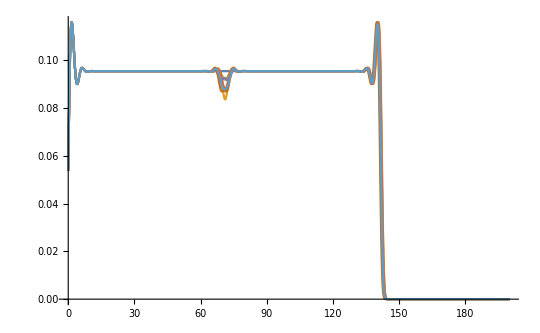

```mathematica
Plot[{ρ0comp[τ,0],ρ1comp[τ,0],ρσ1comp[τ,0],ρσ2comp[τ,0],ρψ1comp[τ,0],ρψ2comp[τ,0],ρϵcomp[τ,0]},{τ,0,200}]
```

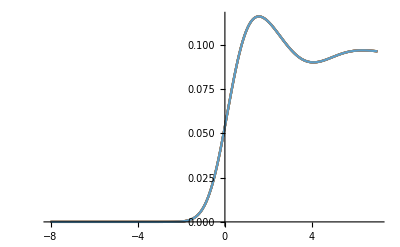

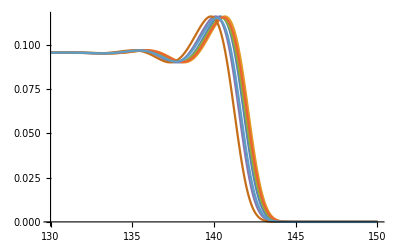

```mathematica
Plot[{ρ0comp[τ,0],ρ1comp[τ,0],ρσ1comp[τ,0],ρσ2comp[τ,0],ρψ1comp[τ,0],ρψ2comp[τ,0],ρϵcomp[τ,0]},{τ,-8,7}]
Plot[{ρ0comp[τ,0],ρ1comp[τ,0],ρσ1comp[τ,0],ρσ2comp[τ,0],ρψ1comp[τ,0],ρψ2comp[τ,0],ρϵcomp[τ,0]},{τ,130,150}]
```

```mathematica
(*τe=N[Length[n0]*2π/lx]*)
Ne=300;
start=110;
end=150;
δk=2π/lx;
τe=(*N[(Length[n0]+1)*2π/lx]*)δk*Ne/ν
N[τe]
```

(500 π)/11

142.8

0.

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.92

0.94

0.96

0.98

1.

1.02

1.04

1.06

1.08

1.1

1.12

1.14

1.16

1.18

1.2

1.22

1.24

1.26

1.28

1.3

1.32

1.34

1.36

1.38

1.4

1.42

1.44

1.46

1.48

1.5

1.52

1.54

1.56

1.58

1.6

1.62

1.64

1.66

1.68

1.7

1.72

1.74

1.76

1.78

1.8

1.82

1.84

1.86

1.88

1.9

1.92

1.94

1.96

1.98

2.

2.02

2.04

2.06

2.08

2.1

2.12

2.14

2.16

2.18

2.2

2.22

2.24

2.26

2.28

2.3

2.32

2.34

2.36

2.38

2.4

2.42

2.44

2.46

2.48

2.5

2.52

2.54

2.56

2.58

2.6

2.62

2.64

2.66

2.68

2.7

2.72

2.74

2.76

2.78

2.8

2.82

2.84

2.86

2.88

2.9

2.92

2.94

2.96

2.98

3.

3.02

3.04

3.06

3.08

3.1

3.12

3.14

3.16

3.18

3.2

3.22

3.24

3.26

3.28

3.3

3.32

3.34

3.36

3.38

3.4

3.42

3.44

3.46

3.48

3.5

3.52

3.54

3.56

3.58

3.6

3.62

3.64

3.66

3.68

3.7

3.72

3.74

3.76

3.78

3.8

3.82

3.84

3.86

3.88

3.9

3.92

3.94

3.96

3.98

4.

4.02

4.04

4.06

4.08

4.1

4.12

4.14

4.16

4.18

4.2

4.22

4.24

4.26

4.28

4.3

4.32

4.34

4.36

4.38

4.4

4.42

4.44

4.46

4.48

4.5

4.52

4.54

4.56

4.58

4.6

4.62

4.64

4.66

4.68

4.7

4.72

4.74

4.76

4.78

4.8

4.82

4.84

4.86

4.88

4.9

4.92

4.94

4.96

4.98

5.

5.02

5.04

5.06

5.08

5.1

5.12

5.14

5.16

5.18

5.2

5.22

5.24

5.26

5.28

5.3

5.32

5.34

5.36

5.38

5.4

5.42

5.44

5.46

5.48

5.5

5.52

5.54

5.56

5.58

5.6

5.62

5.64

5.66

5.68

5.7

5.72

5.74

5.76

5.78

5.8

5.82

5.84

5.86

5.88

5.9

5.92

5.94

5.96

5.98

6.

6.02

6.04

6.06

6.08

6.1

6.12

6.14

6.16

6.18

6.2

6.22

6.24

6.26

6.28

6.3

6.32

6.34

6.36

6.38

6.4

6.42

6.44

6.46

6.48

6.5

6.52

6.54

6.56

6.58

6.6

6.62

6.64

6.66

6.68

6.7

6.72

6.74

6.76

6.78

6.8

6.82

6.84

6.86

6.88

6.9

6.92

6.94

6.96

6.98

7.

7.02

7.04

7.06

7.08

7.1

7.12

7.14

7.16

7.18

7.2

7.22

7.24

7.26

7.28

7.3

7.32

7.34

7.36

7.38

7.4

7.42

7.44

7.46

7.48

7.5

7.52

7.54

7.56

7.58

7.6

7.62

7.64

7.66

7.68

7.7

7.72

7.74

7.76

7.78

7.8

7.82

7.84

7.86

7.88

7.9

7.92

7.94

7.96

7.98

8.

8.02

8.04

8.06

8.08

8.1

8.12

8.14

8.16

8.18

8.2

8.22

8.24

8.26

8.28

8.3

8.32

8.34

8.36

8.38

8.4

8.42

8.44

8.46

8.48

8.5

8.52

8.54

8.56

8.58

8.6

8.62

8.64

8.66

8.68

8.7

8.72

8.74

8.76

8.78

8.8

8.82

8.84

8.86

8.88

8.9

8.92

8.94

8.96

8.98

9.

9.02

9.04

9.06

9.08

9.1

9.12

9.14

9.16

9.18

9.2

9.22

9.24

9.26

9.28

9.3

9.32

9.34

9.36

9.38

9.4

9.42

9.44

9.46

9.48

9.5

9.52

9.54

9.56

9.58

9.6

9.62

9.64

9.66

9.68

9.7

9.72

9.74

9.76

9.78

9.8

9.82

9.84

9.86

9.88

9.9

9.92

9.94

9.96

9.98

10.

10.02

10.04

10.06

10.08

10.1

10.12

10.14

10.16

10.18

10.2

10.22

10.24

10.26

10.28

10.3

10.32

10.34

10.36

10.38

10.4

10.42

10.44

10.46

10.48

10.5

10.52

10.54

10.56

10.58

10.6

10.62

10.64

10.66

10.68

10.7

10.72

10.74

10.76

10.78

10.8

10.82

10.84

10.86

10.88

10.9

10.92

10.94

10.96

10.98

11.

11.02

11.04

11.06

11.08

11.1

11.12

11.14

11.16

11.18

11.2

11.22

11.24

11.26

11.28

11.3

11.32

11.34

11.36

11.38

11.4

11.42

11.44

11.46

11.48

11.5

11.52

11.54

11.56

11.58

11.6

11.62

11.64

11.66

11.68

11.7

11.72

11.74

11.76

11.78

11.8

11.82

11.84

11.86

11.88

11.9

11.92

11.94

11.96

11.98

12.

12.02

12.04

12.06

12.08

12.1

12.12

12.14

12.16

12.18

12.2

12.22

12.24

12.26

12.28

12.3

12.32

12.34

12.36

12.38

12.4

12.42

12.44

12.46

12.48

12.5

12.52

12.54

12.56

12.58

12.6

12.62

12.64

12.66

12.68

12.7

12.72

12.74

12.76

12.78

12.8

12.82

12.84

12.86

12.88

12.9

12.92

12.94

12.96

12.98

13.

13.02

13.04

13.06

13.08

13.1

13.12

13.14

13.16

13.18

13.2

13.22

13.24

13.26

13.28

13.3

13.32

13.34

13.36

13.38

13.4

13.42

13.44

13.46

13.48

13.5

13.52

13.54

13.56

13.58

13.6

13.62

13.64

13.66

13.68

13.7

13.72

13.74

13.76

13.78

13.8

13.82

13.84

13.86

13.88

13.9

13.92

13.94

13.96

13.98

14.

14.02

14.04

14.06

14.08

14.1

14.12

14.14

14.16

14.18

14.2

14.22

14.24

14.26

14.28

14.3

14.32

14.34

14.36

14.38

14.4

14.42

14.44

14.46

14.48

14.5

14.52

14.54

14.56

14.58

14.6

14.62

14.64

14.66

14.68

14.7

14.72

14.74

14.76

14.78

14.8

14.82

14.84

14.86

14.88

14.9

14.92

14.94

14.96

14.98

15.

15.02

15.04

15.06

15.08

15.1

15.12

15.14

15.16

15.18

15.2

15.22

15.24

15.26

15.28

15.3

15.32

15.34

15.36

15.38

15.4

15.42

15.44

15.46

15.48

15.5

15.52

15.54

15.56

15.58

15.6

15.62

15.64

15.66

15.68

15.7

15.72

15.74

15.76

15.78

15.8

15.82

15.84

15.86

15.88

15.9

15.92

15.94

15.96

15.98

16.

16.02

16.04

16.06

16.08

16.1

16.12

16.14

16.16

16.18

16.2

16.22

16.24

16.26

16.28

16.3

16.32

16.34

16.36

16.38

16.4

16.42

16.44

16.46

16.48

16.5

16.52

16.54

16.56

16.58

16.6

16.62

16.64

16.66

16.68

16.7

16.72

16.74

16.76

16.78

16.8

16.82

16.84

16.86

16.88

16.9

16.92

16.94

16.96

16.98

17.

17.02

17.04

17.06

17.08

17.1

17.12

17.14

17.16

17.18

17.2

17.22

17.24

17.26

17.28

17.3

17.32

17.34

17.36

17.38

17.4

17.42

17.44

17.46

17.48

17.5

17.52

17.54

17.56

17.58

17.6

17.62

17.64

17.66

17.68

17.7

17.72

17.74

17.76

17.78

17.8

17.82

17.84

17.86

17.88

17.9

17.92

17.94

17.96

17.98

18.

18.02

18.04

18.06

18.08

18.1

18.12

18.14

18.16

18.18

18.2

18.22

18.24

18.26

18.28

18.3

18.32

18.34

18.36

18.38

18.4

18.42

18.44

18.46

18.48

18.5

18.52

18.54

18.56

18.58

18.6

18.62

18.64

18.66

18.68

18.7

18.72

18.74

18.76

18.78

18.8

18.82

18.84

18.86

18.88

18.9

18.92

18.94

18.96

18.98

19.

19.02

19.04

19.06

19.08

19.1

19.12

19.14

19.16

19.18

19.2

19.22

19.24

19.26

19.28

19.3

19.32

19.34

19.36

19.38

19.4

19.42

19.44

19.46

19.48

19.5

19.52

19.54

19.56

19.58

19.6

19.62

19.64

19.66

19.68

19.7

19.72

19.74

19.76

19.78

19.8

19.82

19.84

19.86

19.88

19.9

19.92

19.94

19.96

19.98

20.

20.02

20.04

20.06

20.08

20.1

20.12

20.14

20.16

20.18

20.2

20.22

20.24

20.26

20.28

20.3

20.32

20.34

20.36

20.38

20.4

20.42

20.44

20.46

20.48

20.5

20.52

20.54

20.56

20.58

20.6

20.62

20.64

20.66

20.68

20.7

20.72

20.74

20.76

20.78

20.8

20.82

20.84

20.86

20.88

20.9

20.92

20.94

20.96

20.98

21.

21.02

21.04

21.06

21.08

21.1

21.12

21.14

21.16

21.18

21.2

21.22

21.24

21.26

21.28

21.3

21.32

21.34

21.36

21.38

21.4

21.42

21.44

21.46

21.48

21.5

21.52

21.54

21.56

21.58

21.6

21.62

21.64

21.66

21.68

21.7

21.72

21.74

21.76

21.78

21.8

21.82

21.84

21.86

21.88

21.9

21.92

21.94

21.96

21.98

22.

22.02

22.04

22.06

22.08

22.1

22.12

22.14

22.16

22.18

22.2

22.22

22.24

22.26

22.28

22.3

22.32

22.34

22.36

22.38

22.4

22.42

22.44

22.46

22.48

22.5

22.52

22.54

22.56

22.58

22.6

22.62

22.64

22.66

22.68

22.7

22.72

22.74

22.76

22.78

22.8

22.82

22.84

22.86

22.88

22.9

22.92

22.94

22.96

22.98

23.

23.02

23.04

23.06

23.08

23.1

23.12

23.14

23.16

23.18

23.2

23.22

23.24

23.26

23.28

23.3

23.32

23.34

23.36

23.38

23.4

23.42

23.44

23.46

23.48

23.5

23.52

23.54

23.56

23.58

23.6

23.62

23.64

23.66

23.68

23.7

23.72

23.74

23.76

23.78

23.8

23.82

23.84

23.86

23.88

23.9

23.92

23.94

23.96

23.98

24.

24.02

24.04

24.06

24.08

24.1

24.12

24.14

24.16

24.18

24.2

24.22

24.24

24.26

24.28

24.3

24.32

24.34

24.36

24.38

24.4

24.42

24.44

24.46

24.48

24.5

24.52

24.54

24.56

24.58

24.6

24.62

24.64

24.66

24.68

24.7

24.72

24.74

24.76

24.78

24.8

24.82

24.84

24.86

24.88

24.9

24.92

24.94

24.96

24.98

25.

25.02

25.04

25.06

25.08

25.1

25.12

25.14

25.16

25.18

25.2

25.22

25.24

25.26

25.28

25.3

25.32

25.34

25.36

25.38

25.4

25.42

25.44

25.46

25.48

25.5

25.52

25.54

25.56

25.58

25.6

25.62

25.64

25.66

25.68

25.7

25.72

25.74

25.76

25.78

25.8

25.82

25.84

25.86

25.88

25.9

25.92

25.94

25.96

25.98

26.

26.02

26.04

26.06

26.08

26.1

26.12

26.14

26.16

26.18

26.2

26.22

26.24

26.26

26.28

26.3

26.32

26.34

26.36

26.38

26.4

26.42

26.44

26.46

26.48

26.5

26.52

26.54

26.56

26.58

26.6

26.62

26.64

26.66

26.68

26.7

26.72

26.74

26.76

26.78

26.8

26.82

26.84

26.86

26.88

26.9

26.92

26.94

26.96

26.98

27.

27.02

27.04

27.06

27.08

27.1

27.12

27.14

27.16

27.18

27.2

27.22

27.24

27.26

27.28

27.3

27.32

27.34

27.36

27.38

27.4

27.42

27.44

27.46

27.48

27.5

27.52

27.54

27.56

27.58

27.6

27.62

27.64

27.66

27.68

27.7

27.72

27.74

27.76

27.78

27.8

27.82

27.84

27.86

27.88

27.9

27.92

27.94

27.96

27.98

28.

28.02

28.04

28.06

28.08

28.1

28.12

28.14

28.16

28.18

28.2

28.22

28.24

28.26

28.28

28.3

28.32

28.34

28.36

28.38

28.4

28.42

28.44

28.46

28.48

28.5

28.52

28.54

28.56

28.58

28.6

28.62

28.64

28.66

28.68

28.7

28.72

28.74

28.76

28.78

28.8

28.82

28.84

28.86

28.88

28.9

28.92

28.94

28.96

28.98

29.

29.02

29.04

29.06

29.08

29.1

29.12

29.14

29.16

29.18

29.2

29.22

29.24

29.26

29.28

29.3

29.32

29.34

29.36

29.38

29.4

29.42

29.44

29.46

29.48

29.5

29.52

29.54

29.56

29.58

29.6

29.62

29.64

29.66

29.68

29.7

29.72

29.74

29.76

29.78

29.8

29.82

29.84

29.86

29.88

29.9

29.92

29.94

29.96

29.98

30.

30.02

30.04

30.06

30.08

30.1

30.12

30.14

30.16

30.18

30.2

30.22

30.24

30.26

30.28

30.3

30.32

30.34

30.36

30.38

30.4

30.42

30.44

30.46

30.48

30.5

30.52

30.54

30.56

30.58

30.6

30.62

30.64

30.66

30.68

30.7

30.72

30.74

30.76

30.78

30.8

30.82

30.84

30.86

30.88

30.9

30.92

30.94

30.96

30.98

31.

31.02

31.04

31.06

31.08

31.1

31.12

31.14

31.16

31.18

31.2

31.22

31.24

31.26

31.28

31.3

31.32

31.34

31.36

31.38

31.4

31.42

31.44

31.46

31.48

31.5

31.52

31.54

31.56

31.58

31.6

31.62

31.64

31.66

31.68

31.7

31.72

31.74

31.76

31.78

31.8

31.82

31.84

31.86

31.88

31.9

31.92

31.94

31.96

31.98

32.

32.02

32.04

32.06

32.08

32.1

32.12

32.14

32.16

32.18

32.2

32.22

32.24

32.26

32.28

32.3

32.32

32.34

32.36

32.38

32.4

32.42

32.44

32.46

32.48

32.5

32.52

32.54

32.56

32.58

32.6

32.62

32.64

32.66

32.68

32.7

32.72

32.74

32.76

32.78

32.8

32.82

32.84

32.86

32.88

32.9

32.92

32.94

32.96

32.98

33.

33.02

33.04

33.06

33.08

33.1

33.12

33.14

33.16

33.18

33.2

33.22

33.24

33.26

33.28

33.3

33.32

33.34

33.36

33.38

33.4

33.42

33.44

33.46

33.48

33.5

33.52

33.54

33.56

33.58

33.6

33.62

33.64

33.66

33.68

33.7

33.72

33.74

33.76

33.78

33.8

33.82

33.84

33.86

33.88

33.9

33.92

33.94

33.96

33.98

34.

34.02

34.04

34.06

34.08

34.1

34.12

34.14

34.16

34.18

34.2

34.22

34.24

34.26

34.28

34.3

34.32

34.34

34.36

34.38

34.4

34.42

34.44

34.46

34.48

34.5

34.52

34.54

34.56

34.58

34.6

34.62

34.64

34.66

34.68

34.7

34.72

34.74

34.76

34.78

34.8

34.82

34.84

34.86

34.88

34.9

34.92

34.94

34.96

34.98

35.

35.02

35.04

35.06

35.08

35.1

35.12

35.14

35.16

35.18

35.2

35.22

35.24

35.26

35.28

35.3

35.32

35.34

35.36

35.38

35.4

35.42

35.44

35.46

35.48

35.5

35.52

35.54

35.56

35.58

35.6

35.62

35.64

35.66

35.68

35.7

35.72

35.74

35.76

35.78

35.8

35.82

35.84

35.86

35.88

35.9

35.92

35.94

35.96

35.98

36.

36.02

36.04

36.06

36.08

36.1

36.12

36.14

36.16

36.18

36.2

36.22

36.24

36.26

36.28

36.3

36.32

36.34

36.36

36.38

36.4

36.42

36.44

36.46

36.48

36.5

36.52

36.54

36.56

36.58

36.6

36.62

36.64

36.66

36.68

36.7

36.72

36.74

36.76

36.78

36.8

36.82

36.84

36.86

36.88

36.9

36.92

36.94

36.96

36.98

37.

37.02

37.04

37.06

37.08

37.1

37.12

37.14

37.16

37.18

37.2

37.22

37.24

37.26

37.28

37.3

37.32

37.34

37.36

37.38

37.4

37.42

37.44

37.46

37.48

37.5

37.52

37.54

37.56

37.58

37.6

37.62

37.64

37.66

37.68

37.7

37.72

37.74

37.76

37.78

37.8

37.82

37.84

37.86

37.88

37.9

37.92

37.94

37.96

37.98

38.

38.02

38.04

38.06

38.08

38.1

38.12

38.14

38.16

38.18

38.2

38.22

38.24

38.26

38.28

38.3

38.32

38.34

38.36

38.38

38.4

38.42

38.44

38.46

38.48

38.5

38.52

38.54

38.56

38.58

38.6

38.62

38.64

38.66

38.68

38.7

38.72

38.74

38.76

38.78

38.8

38.82

38.84

38.86

38.88

38.9

38.92

38.94

38.96

38.98

39.

39.02

39.04

39.06

39.08

39.1

39.12

39.14

39.16

39.18

39.2

39.22

39.24

39.26

39.28

39.3

39.32

39.34

39.36

39.38

39.4

39.42

39.44

39.46

39.48

39.5

39.52

39.54

39.56

39.58

39.6

39.62

39.64

39.66

39.68

39.7

39.72

39.74

39.76

39.78

39.8

39.82

39.84

39.86

39.88

39.9

39.92

39.94

39.96

39.98

40.

40.02

40.04

40.06

40.08

40.1

40.12

40.14

40.16

40.18

40.2

40.22

40.24

40.26

40.28

40.3

40.32

40.34

40.36

40.38

40.4

40.42

40.44

40.46

40.48

40.5

40.52

40.54

40.56

40.58

40.6

40.62

40.64

40.66

40.68

40.7

40.72

40.74

40.76

40.78

40.8

40.82

40.84

40.86

40.88

40.9

40.92

40.94

40.96

40.98

41.

41.02

41.04

41.06

41.08

41.1

41.12

41.14

41.16

41.18

41.2

41.22

41.24

41.26

41.28

41.3

41.32

41.34

41.36

41.38

41.4

41.42

41.44

41.46

41.48

41.5

41.52

41.54

41.56

41.58

41.6

41.62

41.64

41.66

41.68

41.7

41.72

41.74

41.76

41.78

41.8

41.82

41.84

41.86

41.88

41.9

41.92

41.94

41.96

41.98

42.

42.02

42.04

42.06

42.08

42.1

42.12

42.14

42.16

42.18

42.2

42.22

42.24

42.26

42.28

42.3

42.32

42.34

42.36

42.38

42.4

42.42

42.44

42.46

42.48

42.5

42.52

42.54

42.56

42.58

42.6

42.62

42.64

42.66

42.68

42.7

42.72

42.74

42.76

42.78

42.8

42.82

42.84

42.86

42.88

42.9

42.92

42.94

42.96

42.98

43.

43.02

43.04

43.06

43.08

43.1

43.12

43.14

43.16

43.18

43.2

43.22

43.24

43.26

43.28

43.3

43.32

43.34

43.36

43.38

43.4

43.42

43.44

43.46

43.48

43.5

43.52

43.54

43.56

43.58

43.6

43.62

43.64

43.66

43.68

43.7

43.72

43.74

43.76

43.78

43.8

43.82

43.84

43.86

43.88

43.9

43.92

43.94

43.96

43.98

44.

44.02

44.04

44.06

44.08

44.1

44.12

44.14

44.16

44.18

44.2

44.22

44.24

44.26

44.28

44.3

44.32

44.34

44.36

44.38

44.4

44.42

44.44

44.46

44.48

44.5

44.52

44.54

44.56

44.58

44.6

44.62

44.64

44.66

44.68

44.7

44.72

44.74

44.76

44.78

44.8

44.82

44.84

44.86

44.88

44.9

44.92

44.94

44.96

44.98

45.

45.02

45.04

45.06

45.08

45.1

45.12

45.14

45.16

45.18

45.2

45.22

45.24

45.26

45.28

45.3

45.32

45.34

45.36

45.38

45.4

45.42

45.44

45.46

45.48

45.5

45.52

45.54

45.56

45.58

45.6

45.62

45.64

45.66

45.68

45.7

45.72

45.74

45.76

45.78

45.8

45.82

45.84

45.86

45.88

45.9

45.92

45.94

45.96

45.98

46.

46.02

46.04

46.06

46.08

46.1

46.12

46.14

46.16

46.18

46.2

46.22

46.24

46.26

46.28

46.3

46.32

46.34

46.36

46.38

46.4

46.42

46.44

46.46

46.48

46.5

46.52

46.54

46.56

46.58

46.6

46.62

46.64

46.66

46.68

46.7

46.72

46.74

46.76

46.78

46.8

46.82

46.84

46.86

46.88

46.9

46.92

46.94

46.96

46.98

47.

47.02

47.04

47.06

47.08

47.1

47.12

47.14

47.16

47.18

47.2

47.22

47.24

47.26

47.28

47.3

47.32

47.34

47.36

47.38

47.4

47.42

47.44

47.46

47.48

47.5

47.52

47.54

47.56

47.58

47.6

47.62

47.64

47.66

47.68

47.7

47.72

47.74

47.76

47.78

47.8

47.82

47.84

47.86

47.88

47.9

47.92

47.94

47.96

47.98

48.

48.02

48.04

48.06

48.08

48.1

48.12

48.14

48.16

48.18

48.2

48.22

48.24

48.26

48.28

48.3

48.32

48.34

48.36

48.38

48.4

48.42

48.44

48.46

48.48

48.5

48.52

48.54

48.56

48.58

48.6

48.62

48.64

48.66

48.68

48.7

48.72

48.74

48.76

48.78

48.8

48.82

48.84

48.86

48.88

48.9

48.92

48.94

48.96

48.98

49.

49.02

49.04

49.06

49.08

49.1

49.12

49.14

49.16

49.18

49.2

49.22

49.24

49.26

49.28

49.3

49.32

49.34

49.36

49.38

49.4

49.42

49.44

49.46

49.48

49.5

49.52

49.54

49.56

49.58

49.6

49.62

49.64

49.66

49.68

49.7

49.72

49.74

49.76

49.78

49.8

49.82

49.84

49.86

49.88

49.9

49.92

49.94

49.96

49.98

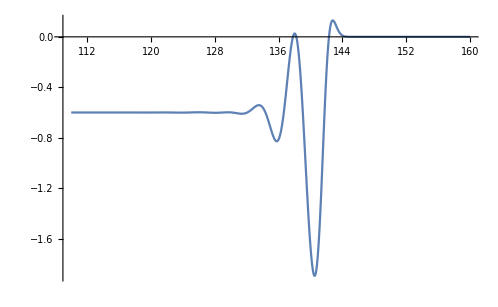

```mathematica
δ=0.02;
integ[start_,end_]:=lx/δk*NIntegrate[(τ-τe)*(ρ1[τ,0]-ρ0300[τ,0]),{τ,start,end}]
oldJe=integ[110,160];
jeList1={{110,oldJe}};
Do[
newJe=oldJe-integ[110+i,110+i+δ];
AppendTo[jeList1,{(110+i+δ),newJe}];
oldJe=newJe;
Print[i];
,{i,0.,50-δ,δ}]
ListLinePlot[jeList1]
```

```mathematica
Export["jeList1v3.csv",jeList1]
```

jeList1v3.csv

0.

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.92

0.94

0.96

0.98

1.

1.02

1.04

1.06

1.08

1.1

1.12

1.14

1.16

1.18

1.2

1.22

1.24

1.26

1.28

1.3

1.32

1.34

1.36

1.38

1.4

1.42

1.44

1.46

1.48

1.5

1.52

1.54

1.56

1.58

1.6

1.62

1.64

1.66

1.68

1.7

1.72

1.74

1.76

1.78

1.8

1.82

1.84

1.86

1.88

1.9

1.92

1.94

1.96

1.98

2.

2.02

2.04

2.06

2.08

2.1

2.12

2.14

2.16

2.18

2.2

2.22

2.24

2.26

2.28

2.3

2.32

2.34

2.36

2.38

2.4

2.42

2.44

2.46

2.48

2.5

2.52

2.54

2.56

2.58

2.6

2.62

2.64

2.66

2.68

2.7

2.72

2.74

2.76

2.78

2.8

2.82

2.84

2.86

2.88

2.9

2.92

2.94

2.96

2.98

3.

3.02

3.04

3.06

3.08

3.1

3.12

3.14

3.16

3.18

3.2

3.22

3.24

3.26

3.28

3.3

3.32

3.34

3.36

3.38

3.4

3.42

3.44

3.46

3.48

3.5

3.52

3.54

3.56

3.58

3.6

3.62

3.64

3.66

3.68

3.7

3.72

3.74

3.76

3.78

3.8

3.82

3.84

3.86

3.88

3.9

3.92

3.94

3.96

3.98

4.

4.02

4.04

4.06

4.08

4.1

4.12

4.14

4.16

4.18

4.2

4.22

4.24

4.26

4.28

4.3

4.32

4.34

4.36

4.38

4.4

4.42

4.44

4.46

4.48

4.5

4.52

4.54

4.56

4.58

4.6

4.62

4.64

4.66

4.68

4.7

4.72

4.74

4.76

4.78

4.8

4.82

4.84

4.86

4.88

4.9

4.92

4.94

4.96

4.98

5.

5.02

5.04

5.06

5.08

5.1

5.12

5.14

5.16

5.18

5.2

5.22

5.24

5.26

5.28

5.3

5.32

5.34

5.36

5.38

5.4

5.42

5.44

5.46

5.48

5.5

5.52

5.54

5.56

5.58

5.6

5.62

5.64

5.66

5.68

5.7

5.72

5.74

5.76

5.78

5.8

5.82

5.84

5.86

5.88

5.9

5.92

5.94

5.96

5.98

6.

6.02

6.04

6.06

6.08

6.1

6.12

6.14

6.16

6.18

6.2

6.22

6.24

6.26

6.28

6.3

6.32

6.34

6.36

6.38

6.4

6.42

6.44

6.46

6.48

6.5

6.52

6.54

6.56

6.58

6.6

6.62

6.64

6.66

6.68

6.7

6.72

6.74

6.76

6.78

6.8

6.82

6.84

6.86

6.88

6.9

6.92

6.94

6.96

6.98

7.

7.02

7.04

7.06

7.08

7.1

7.12

7.14

7.16

7.18

7.2

7.22

7.24

7.26

7.28

7.3

7.32

7.34

7.36

7.38

7.4

7.42

7.44

7.46

7.48

7.5

7.52

7.54

7.56

7.58

7.6

7.62

7.64

7.66

7.68

7.7

7.72

7.74

7.76

7.78

7.8

7.82

7.84

7.86

7.88

7.9

7.92

7.94

7.96

7.98

8.

8.02

8.04

8.06

8.08

8.1

8.12

8.14

8.16

8.18

8.2

8.22

8.24

8.26

8.28

8.3

8.32

8.34

8.36

8.38

8.4

8.42

8.44

8.46

8.48

8.5

8.52

8.54

8.56

8.58

8.6

8.62

8.64

8.66

8.68

8.7

8.72

8.74

8.76

8.78

8.8

8.82

8.84

8.86

8.88

8.9

8.92

8.94

8.96

8.98

9.

9.02

9.04

9.06

9.08

9.1

9.12

9.14

9.16

9.18

9.2

9.22

9.24

9.26

9.28

9.3

9.32

9.34

9.36

9.38

9.4

9.42

9.44

9.46

9.48

9.5

9.52

9.54

9.56

9.58

9.6

9.62

9.64

9.66

9.68

9.7

9.72

9.74

9.76

9.78

9.8

9.82

9.84

9.86

9.88

9.9

9.92

9.94

9.96

9.98

10.

10.02

10.04

10.06

10.08

10.1

10.12

10.14

10.16

10.18

10.2

10.22

10.24

10.26

10.28

10.3

10.32

10.34

10.36

10.38

10.4

10.42

10.44

10.46

10.48

10.5

10.52

10.54

10.56

10.58

10.6

10.62

10.64

10.66

10.68

10.7

10.72

10.74

10.76

10.78

10.8

10.82

10.84

10.86

10.88

10.9

10.92

10.94

10.96

10.98

11.

11.02

11.04

11.06

11.08

11.1

11.12

11.14

11.16

11.18

11.2

11.22

11.24

11.26

11.28

11.3

11.32

11.34

11.36

11.38

11.4

11.42

11.44

11.46

11.48

11.5

11.52

11.54

11.56

11.58

11.6

11.62

11.64

11.66

11.68

11.7

11.72

11.74

11.76

11.78

11.8

11.82

11.84

11.86

11.88

11.9

11.92

11.94

11.96

11.98

12.

12.02

12.04

12.06

12.08

12.1

12.12

12.14

12.16

12.18

12.2

12.22

12.24

12.26

12.28

12.3

12.32

12.34

12.36

12.38

12.4

12.42

12.44

12.46

12.48

12.5

12.52

12.54

12.56

12.58

12.6

12.62

12.64

12.66

12.68

12.7

12.72

12.74

12.76

12.78

12.8

12.82

12.84

12.86

12.88

12.9

12.92

12.94

12.96

12.98

13.

13.02

13.04

13.06

13.08

13.1

13.12

13.14

13.16

13.18

13.2

13.22

13.24

13.26

13.28

13.3

13.32

13.34

13.36

13.38

13.4

13.42

13.44

13.46

13.48

13.5

13.52

13.54

13.56

13.58

13.6

13.62

13.64

13.66

13.68

13.7

13.72

13.74

13.76

13.78

13.8

13.82

13.84

13.86

13.88

13.9

13.92

13.94

13.96

13.98

14.

14.02

14.04

14.06

14.08

14.1

14.12

14.14

14.16

14.18

14.2

14.22

14.24

14.26

14.28

14.3

14.32

14.34

14.36

14.38

14.4

14.42

14.44

14.46

14.48

14.5

14.52

14.54

14.56

14.58

14.6

14.62

14.64

14.66

14.68

14.7

14.72

14.74

14.76

14.78

14.8

14.82

14.84

14.86

14.88

14.9

14.92

14.94

14.96

14.98

15.

15.02

15.04

15.06

15.08

15.1

15.12

15.14

15.16

15.18

15.2

15.22

15.24

15.26

15.28

15.3

15.32

15.34

15.36

15.38

15.4

15.42

15.44

15.46

15.48

15.5

15.52

15.54

15.56

15.58

15.6

15.62

15.64

15.66

15.68

15.7

15.72

15.74

15.76

15.78

15.8

15.82

15.84

15.86

15.88

15.9

15.92

15.94

15.96

15.98

16.

16.02

16.04

16.06

16.08

16.1

16.12

16.14

16.16

16.18

16.2

16.22

16.24

16.26

16.28

16.3

16.32

16.34

16.36

16.38

16.4

16.42

16.44

16.46

16.48

16.5

16.52

16.54

16.56

16.58

16.6

16.62

16.64

16.66

16.68

16.7

16.72

16.74

16.76

16.78

16.8

16.82

16.84

16.86

16.88

16.9

16.92

16.94

16.96

16.98

17.

17.02

17.04

17.06

17.08

17.1

17.12

17.14

17.16

17.18

17.2

17.22

17.24

17.26

17.28

17.3

17.32

17.34

17.36

17.38

17.4

17.42

17.44

17.46

17.48

17.5

17.52

17.54

17.56

17.58

17.6

17.62

17.64

17.66

17.68

17.7

17.72

17.74

17.76

17.78

17.8

17.82

17.84

17.86

17.88

17.9

17.92

17.94

17.96

17.98

18.

18.02

18.04

18.06

18.08

18.1

18.12

18.14

18.16

18.18

18.2

18.22

18.24

18.26

18.28

18.3

18.32

18.34

18.36

18.38

18.4

18.42

18.44

18.46

18.48

18.5

18.52

18.54

18.56

18.58

18.6

18.62

18.64

18.66

18.68

18.7

18.72

18.74

18.76

18.78

18.8

18.82

18.84

18.86

18.88

18.9

18.92

18.94

18.96

18.98

19.

19.02

19.04

19.06

19.08

19.1

19.12

19.14

19.16

19.18

19.2

19.22

19.24

19.26

19.28

19.3

19.32

19.34

19.36

19.38

19.4

19.42

19.44

19.46

19.48

19.5

19.52

19.54

19.56

19.58

19.6

19.62

19.64

19.66

19.68

19.7

19.72

19.74

19.76

19.78

19.8

19.82

19.84

19.86

19.88

19.9

19.92

19.94

19.96

19.98

20.

20.02

20.04

20.06

20.08

20.1

20.12

20.14

20.16

20.18

20.2

20.22

20.24

20.26

20.28

20.3

20.32

20.34

20.36

20.38

20.4

20.42

20.44

20.46

20.48

20.5

20.52

20.54

20.56

20.58

20.6

20.62

20.64

20.66

20.68

20.7

20.72

20.74

20.76

20.78

20.8

20.82

20.84

20.86

20.88

20.9

20.92

20.94

20.96

20.98

21.

21.02

21.04

21.06

21.08

21.1

21.12

21.14

21.16

21.18

21.2

21.22

21.24

21.26

21.28

21.3

21.32

21.34

21.36

21.38

21.4

21.42

21.44

21.46

21.48

21.5

21.52

21.54

21.56

21.58

21.6

21.62

21.64

21.66

21.68

21.7

21.72

21.74

21.76

21.78

21.8

21.82

21.84

21.86

21.88

21.9

21.92

21.94

21.96

21.98

22.

22.02

22.04

22.06

22.08

22.1

22.12

22.14

22.16

22.18

22.2

22.22

22.24

22.26

22.28

22.3

22.32

22.34

22.36

22.38

22.4

22.42

22.44

22.46

22.48

22.5

22.52

22.54

22.56

22.58

22.6

22.62

22.64

22.66

22.68

22.7

22.72

22.74

22.76

22.78

22.8

22.82

22.84

22.86

22.88

22.9

22.92

22.94

22.96

22.98

23.

23.02

23.04

23.06

23.08

23.1

23.12

23.14

23.16

23.18

23.2

23.22

23.24

23.26

23.28

23.3

23.32

23.34

23.36

23.38

23.4

23.42

23.44

23.46

23.48

23.5

23.52

23.54

23.56

23.58

23.6

23.62

23.64

23.66

23.68

23.7

23.72

23.74

23.76

23.78

23.8

23.82

23.84

23.86

23.88

23.9

23.92

23.94

23.96

23.98

24.

24.02

24.04

24.06

24.08

24.1

24.12

24.14

24.16

24.18

24.2

24.22

24.24

24.26

24.28

24.3

24.32

24.34

24.36

24.38

24.4

24.42

24.44

24.46

24.48

24.5

24.52

24.54

24.56

24.58

24.6

24.62

24.64

24.66

24.68

24.7

24.72

24.74

24.76

24.78

24.8

24.82

24.84

24.86

24.88

24.9

24.92

24.94

24.96

24.98

25.

25.02

25.04

25.06

25.08

25.1

25.12

25.14

25.16

25.18

25.2

25.22

25.24

25.26

25.28

25.3

25.32

25.34

25.36

25.38

25.4

25.42

25.44

25.46

25.48

25.5

25.52

25.54

25.56

25.58

25.6

25.62

25.64

25.66

25.68

25.7

25.72

25.74

25.76

25.78

25.8

25.82

25.84

25.86

25.88

25.9

25.92

25.94

25.96

25.98

26.

26.02

26.04

26.06

26.08

26.1

26.12

26.14

26.16

26.18

26.2

26.22

26.24

26.26

26.28

26.3

26.32

26.34

26.36

26.38

26.4

26.42

26.44

26.46

26.48

26.5

26.52

26.54

26.56

26.58

26.6

26.62

26.64

26.66

26.68

26.7

26.72

26.74

26.76

26.78

26.8

26.82

26.84

26.86

26.88

26.9

26.92

26.94

26.96

26.98

27.

27.02

27.04

27.06

27.08

27.1

27.12

27.14

27.16

27.18

27.2

27.22

27.24

27.26

27.28

27.3

27.32

27.34

27.36

27.38

27.4

27.42

27.44

27.46

27.48

27.5

27.52

27.54

27.56

27.58

27.6

27.62

27.64

27.66

27.68

27.7

27.72

27.74

27.76

27.78

27.8

27.82

27.84

27.86

27.88

27.9

27.92

27.94

27.96

27.98

28.

28.02

28.04

28.06

28.08

28.1

28.12

28.14

28.16

28.18

28.2

28.22

28.24

28.26

28.28

28.3

28.32

28.34

28.36

28.38

28.4

28.42

28.44

28.46

28.48

28.5

28.52

28.54

28.56

28.58

28.6

28.62

28.64

28.66

28.68

28.7

28.72

28.74

28.76

28.78

28.8

28.82

28.84

28.86

28.88

28.9

28.92

28.94

28.96

28.98

29.

29.02

29.04

29.06

29.08

29.1

29.12

29.14

29.16

29.18

29.2

29.22

29.24

29.26

29.28

29.3

29.32

29.34

29.36

29.38

29.4

29.42

29.44

29.46

29.48

29.5

29.52

29.54

29.56

29.58

29.6

29.62

29.64

29.66

29.68

29.7

29.72

29.74

29.76

29.78

29.8

29.82

29.84

29.86

29.88

29.9

29.92

29.94

29.96

29.98

30.

30.02

30.04

30.06

30.08

30.1

30.12

30.14

30.16

30.18

30.2

30.22

30.24

30.26

30.28

30.3

30.32

30.34

30.36

30.38

30.4

30.42

30.44

30.46

30.48

30.5

30.52

30.54

30.56

30.58

30.6

30.62

30.64

30.66

30.68

30.7

30.72

30.74

30.76

30.78

30.8

30.82

30.84

30.86

30.88

30.9

30.92

30.94

30.96

30.98

31.

31.02

31.04

31.06

31.08

31.1

31.12

31.14

31.16

31.18

31.2

31.22

31.24

31.26

31.28

31.3

31.32

31.34

31.36

31.38

31.4

31.42

31.44

31.46

31.48

31.5

31.52

31.54

31.56

31.58

31.6

31.62

31.64

31.66

31.68

31.7

31.72

31.74

31.76

31.78

31.8

31.82

31.84

31.86

31.88

31.9

31.92

31.94

31.96

31.98

32.

32.02

32.04

32.06

32.08

32.1

32.12

32.14

32.16

32.18

32.2

32.22

32.24

32.26

32.28

32.3

32.32

32.34

32.36

32.38

32.4

32.42

32.44

32.46

32.48

32.5

32.52

32.54

32.56

32.58

32.6

32.62

32.64

32.66

32.68

32.7

32.72

32.74

32.76

32.78

32.8

32.82

32.84

32.86

32.88

32.9

32.92

32.94

32.96

32.98

33.

33.02

33.04

33.06

33.08

33.1

33.12

33.14

33.16

33.18

33.2

33.22

33.24

33.26

33.28

33.3

33.32

33.34

33.36

33.38

33.4

33.42

33.44

33.46

33.48

33.5

33.52

33.54

33.56

33.58

33.6

33.62

33.64

33.66

33.68

33.7

33.72

33.74

33.76

33.78

33.8

33.82

33.84

33.86

33.88

33.9

33.92

33.94

33.96

33.98

34.

34.02

34.04

34.06

34.08

34.1

34.12

34.14

34.16

34.18

34.2

34.22

34.24

34.26

34.28

34.3

34.32

34.34

34.36

34.38

34.4

34.42

34.44

34.46

34.48

34.5

34.52

34.54

34.56

34.58

34.6

34.62

34.64

34.66

34.68

34.7

34.72

34.74

34.76

34.78

34.8

34.82

34.84

34.86

34.88

34.9

34.92

34.94

34.96

34.98

35.

35.02

35.04

35.06

35.08

35.1

35.12

35.14

35.16

35.18

35.2

35.22

35.24

35.26

35.28

35.3

35.32

35.34

35.36

35.38

35.4

35.42

35.44

35.46

35.48

35.5

35.52

35.54

35.56

35.58

35.6

35.62

35.64

35.66

35.68

35.7

35.72

35.74

35.76

35.78

35.8

35.82

35.84

35.86

35.88

35.9

35.92

35.94

35.96

35.98

36.

36.02

36.04

36.06

36.08

36.1

36.12

36.14

36.16

36.18

36.2

36.22

36.24

36.26

36.28

36.3

36.32

36.34

36.36

36.38

36.4

36.42

36.44

36.46

36.48

36.5

36.52

36.54

36.56

36.58

36.6

36.62

36.64

36.66

36.68

36.7

36.72

36.74

36.76

36.78

36.8

36.82

36.84

36.86

36.88

36.9

36.92

36.94

36.96

36.98

37.

37.02

37.04

37.06

37.08

37.1

37.12

37.14

37.16

37.18

37.2

37.22

37.24

37.26

37.28

37.3

37.32

37.34

37.36

37.38

37.4

37.42

37.44

37.46

37.48

37.5

37.52

37.54

37.56

37.58

37.6

37.62

37.64

37.66

37.68

37.7

37.72

37.74

37.76

37.78

37.8

37.82

37.84

37.86

37.88

37.9

37.92

37.94

37.96

37.98

38.

38.02

38.04

38.06

38.08

38.1

38.12

38.14

38.16

38.18

38.2

38.22

38.24

38.26

38.28

38.3

38.32

38.34

38.36

38.38

38.4

38.42

38.44

38.46

38.48

38.5

38.52

38.54

38.56

38.58

38.6

38.62

38.64

38.66

38.68

38.7

38.72

38.74

38.76

38.78

38.8

38.82

38.84

38.86

38.88

38.9

38.92

38.94

38.96

38.98

39.

39.02

39.04

39.06

39.08

39.1

39.12

39.14

39.16

39.18

39.2

39.22

39.24

39.26

39.28

39.3

39.32

39.34

39.36

39.38

39.4

39.42

39.44

39.46

39.48

39.5

39.52

39.54

39.56

39.58

39.6

39.62

39.64

39.66

39.68

39.7

39.72

39.74

39.76

39.78

39.8

39.82

39.84

39.86

39.88

39.9

39.92

39.94

39.96

39.98

40.

40.02

40.04

40.06

40.08

40.1

40.12

40.14

40.16

40.18

40.2

40.22

40.24

40.26

40.28

40.3

40.32

40.34

40.36

40.38

40.4

40.42

40.44

40.46

40.48

40.5

40.52

40.54

40.56

40.58

40.6

40.62

40.64

40.66

40.68

40.7

40.72

40.74

40.76

40.78

40.8

40.82

40.84

40.86

40.88

40.9

40.92

40.94

40.96

40.98

41.

41.02

41.04

41.06

41.08

41.1

41.12

41.14

41.16

41.18

41.2

41.22

41.24

41.26

41.28

41.3

41.32

41.34

41.36

41.38

41.4

41.42

41.44

41.46

41.48

41.5

41.52

41.54

41.56

41.58

41.6

41.62

41.64

41.66

41.68

41.7

41.72

41.74

41.76

41.78

41.8

41.82

41.84

41.86

41.88

41.9

41.92

41.94

41.96

41.98

42.

42.02

42.04

42.06

42.08

42.1

42.12

42.14

42.16

42.18

42.2

42.22

42.24

42.26

42.28

42.3

42.32

42.34

42.36

42.38

42.4

42.42

42.44

42.46

42.48

42.5

42.52

42.54

42.56

42.58

42.6

42.62

42.64

42.66

42.68

42.7

42.72

42.74

42.76

42.78

42.8

42.82

42.84

42.86

42.88

42.9

42.92

42.94

42.96

42.98

43.

43.02

43.04

43.06

43.08

43.1

43.12

43.14

43.16

43.18

43.2

43.22

43.24

43.26

43.28

43.3

43.32

43.34

43.36

43.38

43.4

43.42

43.44

43.46

43.48

43.5

43.52

43.54

43.56

43.58

43.6

43.62

43.64

43.66

43.68

43.7

43.72

43.74

43.76

43.78

43.8

43.82

43.84

43.86

43.88

43.9

43.92

43.94

43.96

43.98

44.

44.02

44.04

44.06

44.08

44.1

44.12

44.14

44.16

44.18

44.2

44.22

44.24

44.26

44.28

44.3

44.32

44.34

44.36

44.38

44.4

44.42

44.44

44.46

44.48

44.5

44.52

44.54

44.56

44.58

44.6

44.62

44.64

44.66

44.68

44.7

44.72

44.74

44.76

44.78

44.8

44.82

44.84

44.86

44.88

44.9

44.92

44.94

44.96

44.98

45.

45.02

45.04

45.06

45.08

45.1

45.12

45.14

45.16

45.18

45.2

45.22

45.24

45.26

45.28

45.3

45.32

45.34

45.36

45.38

45.4

45.42

45.44

45.46

45.48

45.5

45.52

45.54

45.56

45.58

45.6

45.62

45.64

45.66

45.68

45.7

45.72

45.74

45.76

45.78

45.8

45.82

45.84

45.86

45.88

45.9

45.92

45.94

45.96

45.98

46.

46.02

46.04

46.06

46.08

46.1

46.12

46.14

46.16

46.18

46.2

46.22

46.24

46.26

46.28

46.3

46.32

46.34

46.36

46.38

46.4

46.42

46.44

46.46

46.48

46.5

46.52

46.54

46.56

46.58

46.6

46.62

46.64

46.66

46.68

46.7

46.72

46.74

46.76

46.78

46.8

46.82

46.84

46.86

46.88

46.9

46.92

46.94

46.96

46.98

47.

47.02

47.04

47.06

47.08

47.1

47.12

47.14

47.16

47.18

47.2

47.22

47.24

47.26

47.28

47.3

47.32

47.34

47.36

47.38

47.4

47.42

47.44

47.46

47.48

47.5

47.52

47.54

47.56

47.58

47.6

47.62

47.64

47.66

47.68

47.7

47.72

47.74

47.76

47.78

47.8

47.82

47.84

47.86

47.88

47.9

47.92

47.94

47.96

47.98

48.

48.02

48.04

48.06

48.08

48.1

48.12

48.14

48.16

48.18

48.2

48.22

48.24

48.26

48.28

48.3

48.32

48.34

48.36

48.38

48.4

48.42

48.44

48.46

48.48

48.5

48.52

48.54

48.56

48.58

48.6

48.62

48.64

48.66

48.68

48.7

48.72

48.74

48.76

48.78

48.8

48.82

48.84

48.86

48.88

48.9

48.92

48.94

48.96

48.98

49.

49.02

49.04

49.06

49.08

49.1

49.12

49.14

49.16

49.18

49.2

49.22

49.24

49.26

49.28

49.3

49.32

49.34

49.36

49.38

49.4

49.42

49.44

49.46

49.48

49.5

49.52

49.54

49.56

49.58

49.6

49.62

49.64

49.66

49.68

49.7

49.72

49.74

49.76

49.78

49.8

49.82

49.84

49.86

49.88

49.9

49.92

49.94

49.96

49.98

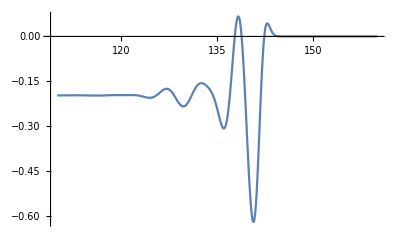

jeListsigma1v3.csv

{{110,-0.197242},{130.,-0.231618},{150.,-2.38698×10^-14}}

```mathematica
integ[start_,end_]:=lx/δk*NIntegrate[(τ-τe)*(ρσ1[τ,0]-ρ0300[τ,0]),{τ,start,end}]
oldJe=integ[110,160];
jeListσ1={{110,oldJe}};
Do[
newJe=oldJe-integ[110+i,110+i+δ];
AppendTo[jeListσ1,{(110+i+δ),newJe}];
oldJe=newJe;
Print[i];
,{i,0.,50-δ,δ}]
ListLinePlot[jeListσ1]
Export["jeListsigma1v3.csv",jeListσ1]
```

0.

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.92

0.94

0.96

0.98

1.

1.02

1.04

1.06

1.08

1.1

1.12

1.14

1.16

1.18

1.2

1.22

1.24

1.26

1.28

1.3

1.32

1.34

1.36

1.38

1.4

1.42

1.44

1.46

1.48

1.5

1.52

1.54

1.56

1.58

1.6

1.62

1.64

1.66

1.68

1.7

1.72

1.74

1.76

1.78

1.8

1.82

1.84

1.86

1.88

1.9

1.92

1.94

1.96

1.98

2.

2.02

2.04

2.06

2.08

2.1

2.12

2.14

2.16

2.18

2.2

2.22

2.24

2.26

2.28

2.3

2.32

2.34

2.36

2.38

2.4

2.42

2.44

2.46

2.48

2.5

2.52

2.54

2.56

2.58

2.6

2.62

2.64

2.66

2.68

2.7

2.72

2.74

2.76

2.78

2.8

2.82

2.84

2.86

2.88

2.9

2.92

2.94

2.96

2.98

3.

3.02

3.04

3.06

3.08

3.1

3.12

3.14

3.16

3.18

3.2

3.22

3.24

3.26

3.28

3.3

3.32

3.34

3.36

3.38

3.4

3.42

3.44

3.46

3.48

3.5

3.52

3.54

3.56

3.58

3.6

3.62

3.64

3.66

3.68

3.7

3.72

3.74

3.76

3.78

3.8

3.82

3.84

3.86

3.88

3.9

3.92

3.94

3.96

3.98

4.

4.02

4.04

4.06

4.08

4.1

4.12

4.14

4.16

4.18

4.2

4.22

4.24

4.26

4.28

4.3

4.32

4.34

4.36

4.38

4.4

4.42

4.44

4.46

4.48

4.5

4.52

4.54

4.56

4.58

4.6

4.62

4.64

4.66

4.68

4.7

4.72

4.74

4.76

4.78

4.8

4.82

4.84

4.86

4.88

4.9

4.92

4.94

4.96

4.98

5.

5.02

5.04

5.06

5.08

5.1

5.12

5.14

5.16

5.18

5.2

5.22

5.24

5.26

5.28

5.3

5.32

5.34

5.36

5.38

5.4

5.42

5.44

5.46

5.48

5.5

5.52

5.54

5.56

5.58

5.6

5.62

5.64

5.66

5.68

5.7

5.72

5.74

5.76

5.78

5.8

5.82

5.84

5.86

5.88

5.9

5.92

5.94

5.96

5.98

6.

6.02

6.04

6.06

6.08

6.1

6.12

6.14

6.16

6.18

6.2

6.22

6.24

6.26

6.28

6.3

6.32

6.34

6.36

6.38

6.4

6.42

6.44

6.46

6.48

6.5

6.52

6.54

6.56

6.58

6.6

6.62

6.64

6.66

6.68

6.7

6.72

6.74

6.76

6.78

6.8

6.82

6.84

6.86

6.88

6.9

6.92

6.94

6.96

6.98

7.

7.02

7.04

7.06

7.08

7.1

7.12

7.14

7.16

7.18

7.2

7.22

7.24

7.26

7.28

7.3

7.32

7.34

7.36

7.38

7.4

7.42

7.44

7.46

7.48

7.5

7.52

7.54

7.56

7.58

7.6

7.62

7.64

7.66

7.68

7.7

7.72

7.74

7.76

7.78

7.8

7.82

7.84

7.86

7.88

7.9

7.92

7.94

7.96

7.98

8.

8.02

8.04

8.06

8.08

8.1

8.12

8.14

8.16

8.18

8.2

8.22

8.24

8.26

8.28

8.3

8.32

8.34

8.36

8.38

8.4

8.42

8.44

8.46

8.48

8.5

8.52

8.54

8.56

8.58

8.6

8.62

8.64

8.66

8.68

8.7

8.72

8.74

8.76

8.78

8.8

8.82

8.84

8.86

8.88

8.9

8.92

8.94

8.96

8.98

9.

9.02

9.04

9.06

9.08

9.1

9.12

9.14

9.16

9.18

9.2

9.22

9.24

9.26

9.28

9.3

9.32

9.34

9.36

9.38

9.4

9.42

9.44

9.46

9.48

9.5

9.52

9.54

9.56

9.58

9.6

9.62

9.64

9.66

9.68

9.7

9.72

9.74

9.76

9.78

9.8

9.82

9.84

9.86

9.88

9.9

9.92

9.94

9.96

9.98

10.

10.02

10.04

10.06

10.08

10.1

10.12

10.14

10.16

10.18

10.2

10.22

10.24

10.26

10.28

10.3

10.32

10.34

10.36

10.38

10.4

10.42

10.44

10.46

10.48

10.5

10.52

10.54

10.56

10.58

10.6

10.62

10.64

10.66

10.68

10.7

10.72

10.74

10.76

10.78

10.8

10.82

10.84

10.86

10.88

10.9

10.92

10.94

10.96

10.98

11.

11.02

11.04

11.06

11.08

11.1

11.12

11.14

11.16

11.18

11.2

11.22

11.24

11.26

11.28

11.3

11.32

11.34

11.36

11.38

11.4

11.42

11.44

11.46

11.48

11.5

11.52

11.54

11.56

11.58

11.6

11.62

11.64

11.66

11.68

11.7

11.72

11.74

11.76

11.78

11.8

11.82

11.84

11.86

11.88

11.9

11.92

11.94

11.96

11.98

12.

12.02

12.04

12.06

12.08

12.1

12.12

12.14

12.16

12.18

12.2

12.22

12.24

12.26

12.28

12.3

12.32

12.34

12.36

12.38

12.4

12.42

12.44

12.46

12.48

12.5

12.52

12.54

12.56

12.58

12.6

12.62

12.64

12.66

12.68

12.7

12.72

12.74

12.76

12.78

12.8

12.82

12.84

12.86

12.88

12.9

12.92

12.94

12.96

12.98

13.

13.02

13.04

13.06

13.08

13.1

13.12

13.14

13.16

13.18

13.2

13.22

13.24

13.26

13.28

13.3

13.32

13.34

13.36

13.38

13.4

13.42

13.44

13.46

13.48

13.5

13.52

13.54

13.56

13.58

13.6

13.62

13.64

13.66

13.68

13.7

13.72

13.74

13.76

13.78

13.8

13.82

13.84

13.86

13.88

13.9

13.92

13.94

13.96

13.98

14.

14.02

14.04

14.06

14.08

14.1

14.12

14.14

14.16

14.18

14.2

14.22

14.24

14.26

14.28

14.3

14.32

14.34

14.36

14.38

14.4

14.42

14.44

14.46

14.48

14.5

14.52

14.54

14.56

14.58

14.6

14.62

14.64

14.66

14.68

14.7

14.72

14.74

14.76

14.78

14.8

14.82

14.84

14.86

14.88

14.9

14.92

14.94

14.96

14.98

15.

15.02

15.04

15.06

15.08

15.1

15.12

15.14

15.16

15.18

15.2

15.22

15.24

15.26

15.28

15.3

15.32

15.34

15.36

15.38

15.4

15.42

15.44

15.46

15.48

15.5

15.52

15.54

15.56

15.58

15.6

15.62

15.64

15.66

15.68

15.7

15.72

15.74

15.76

15.78

15.8

15.82

15.84

15.86

15.88

15.9

15.92

15.94

15.96

15.98

16.

16.02

16.04

16.06

16.08

16.1

16.12

16.14

16.16

16.18

16.2

16.22

16.24

16.26

16.28

16.3

16.32

16.34

16.36

16.38

16.4

16.42

16.44

16.46

16.48

16.5

16.52

16.54

16.56

16.58

16.6

16.62

16.64

16.66

16.68

16.7

16.72

16.74

16.76

16.78

16.8

16.82

16.84

16.86

16.88

16.9

16.92

16.94

16.96

16.98

17.

17.02

17.04

17.06

17.08

17.1

17.12

17.14

17.16

17.18

17.2

17.22

17.24

17.26

17.28

17.3

17.32

17.34

17.36

17.38

17.4

17.42

17.44

17.46

17.48

17.5

17.52

17.54

17.56

17.58

17.6

17.62

17.64

17.66

17.68

17.7

17.72

17.74

17.76

17.78

17.8

17.82

17.84

17.86

17.88

17.9

17.92

17.94

17.96

17.98

18.

18.02

18.04

18.06

18.08

18.1

18.12

18.14

18.16

18.18

18.2

18.22

18.24

18.26

18.28

18.3

18.32

18.34

18.36

18.38

18.4

18.42

18.44

18.46

18.48

18.5

18.52

18.54

18.56

18.58

18.6

18.62

18.64

18.66

18.68

18.7

18.72

18.74

18.76

18.78

18.8

18.82

18.84

18.86

18.88

18.9

18.92

18.94

18.96

18.98

19.

19.02

19.04

19.06

19.08

19.1

19.12

19.14

19.16

19.18

19.2

19.22

19.24

19.26

19.28

19.3

19.32

19.34

19.36

19.38

19.4

19.42

19.44

19.46

19.48

19.5

19.52

19.54

19.56

19.58

19.6

19.62

19.64

19.66

19.68

19.7

19.72

19.74

19.76

19.78

19.8

19.82

19.84

19.86

19.88

19.9

19.92

19.94

19.96

19.98

20.

20.02

20.04

20.06

20.08

20.1

20.12

20.14

20.16

20.18

20.2

20.22

20.24

20.26

20.28

20.3

20.32

20.34

20.36

20.38

20.4

20.42

20.44

20.46

20.48

20.5

20.52

20.54

20.56

20.58

20.6

20.62

20.64

20.66

20.68

20.7

20.72

20.74

20.76

20.78

20.8

20.82

20.84

20.86

20.88

20.9

20.92

20.94

20.96

20.98

21.

21.02

21.04

21.06

21.08

21.1

21.12

21.14

21.16

21.18

21.2

21.22

21.24

21.26

21.28

21.3

21.32

21.34

21.36

21.38

21.4

21.42

21.44

21.46

21.48

21.5

21.52

21.54

21.56

21.58

21.6

21.62

21.64

21.66

21.68

21.7

21.72

21.74

21.76

21.78

21.8

21.82

21.84

21.86

21.88

21.9

21.92

21.94

21.96

21.98

22.

22.02

22.04

22.06

22.08

22.1

22.12

22.14

22.16

22.18

22.2

22.22

22.24

22.26

22.28

22.3

22.32

22.34

22.36

22.38

22.4

22.42

22.44

22.46

22.48

22.5

22.52

22.54

22.56

22.58

22.6

22.62

22.64

22.66

22.68

22.7

22.72

22.74

22.76

22.78

22.8

22.82

22.84

22.86

22.88

22.9

22.92

22.94

22.96

22.98

23.

23.02

23.04

23.06

23.08

23.1

23.12

23.14

23.16

23.18

23.2

23.22

23.24

23.26

23.28

23.3

23.32

23.34

23.36

23.38

23.4

23.42

23.44

23.46

23.48

23.5

23.52

23.54

23.56

23.58

23.6

23.62

23.64

23.66

23.68

23.7

23.72

23.74

23.76

23.78

23.8

23.82

23.84

23.86

23.88

23.9

23.92

23.94

23.96

23.98

24.

24.02

24.04

24.06

24.08

24.1

24.12

24.14

24.16

24.18

24.2

24.22

24.24

24.26

24.28

24.3

24.32

24.34

24.36

24.38

24.4

24.42

24.44

24.46

24.48

24.5

24.52

24.54

24.56

24.58

24.6

24.62

24.64

24.66

24.68

24.7

24.72

24.74

24.76

24.78

24.8

24.82

24.84

24.86

24.88

24.9

24.92

24.94

24.96

24.98

25.

25.02

25.04

25.06

25.08

25.1

25.12

25.14

25.16

25.18

25.2

25.22

25.24

25.26

25.28

25.3

25.32

25.34

25.36

25.38

25.4

25.42

25.44

25.46

25.48

25.5

25.52

25.54

25.56

25.58

25.6

25.62

25.64

25.66

25.68

25.7

25.72

25.74

25.76

25.78

25.8

25.82

25.84

25.86

25.88

25.9

25.92

25.94

25.96

25.98

26.

26.02

26.04

26.06

26.08

26.1

26.12

26.14

26.16

26.18

26.2

26.22

26.24

26.26

26.28

26.3

26.32

26.34

26.36

26.38

26.4

26.42

26.44

26.46

26.48

26.5

26.52

26.54

26.56

26.58

26.6

26.62

26.64

26.66

26.68

26.7

26.72

26.74

26.76

26.78

26.8

26.82

26.84

26.86

26.88

26.9

26.92

26.94

26.96

26.98

27.

27.02

27.04

27.06

27.08

27.1

27.12

27.14

27.16

27.18

27.2

27.22

27.24

27.26

27.28

27.3

27.32

27.34

27.36

27.38

27.4

27.42

27.44

27.46

27.48

27.5

27.52

27.54

27.56

27.58

27.6

27.62

27.64

27.66

27.68

27.7

27.72

27.74

27.76

27.78

27.8

27.82

27.84

27.86

27.88

27.9

27.92

27.94

27.96

27.98

28.

28.02

28.04

28.06

28.08

28.1

28.12

28.14

28.16

28.18

28.2

28.22

28.24

28.26

28.28

28.3

28.32

28.34

28.36

28.38

28.4

28.42

28.44

28.46

28.48

28.5

28.52

28.54

28.56

28.58

28.6

28.62

28.64

28.66

28.68

28.7

28.72

28.74

28.76

28.78

28.8

28.82

28.84

28.86

28.88

28.9

28.92

28.94

28.96

28.98

29.

29.02

29.04

29.06

29.08

29.1

29.12

29.14

29.16

29.18

29.2

29.22

29.24

29.26

29.28

29.3

29.32

29.34

29.36

29.38

29.4

29.42

29.44

29.46

29.48

29.5

29.52

29.54

29.56

29.58

29.6

29.62

29.64

29.66

29.68

29.7

29.72

29.74

29.76

29.78

29.8

29.82

29.84

29.86

29.88

29.9

29.92

29.94

29.96

29.98

30.

30.02

30.04

30.06

30.08

30.1

30.12

30.14

30.16

30.18

30.2

30.22

30.24

30.26

30.28

30.3

30.32

30.34

30.36

30.38

30.4

30.42

30.44

30.46

30.48

30.5

30.52

30.54

30.56

30.58

30.6

30.62

30.64

30.66

30.68

30.7

30.72

30.74

30.76

30.78

30.8

30.82

30.84

30.86

30.88

30.9

30.92

30.94

30.96

30.98

31.

31.02

31.04

31.06

31.08

31.1

31.12

31.14

31.16

31.18

31.2

31.22

31.24

31.26

31.28

31.3

31.32

31.34

31.36

31.38

31.4

31.42

31.44

31.46

31.48

31.5

31.52

31.54

31.56

31.58

31.6

31.62

31.64

31.66

31.68

31.7

31.72

31.74

31.76

31.78

31.8

31.82

31.84

31.86

31.88

31.9

31.92

31.94

31.96

31.98

32.

32.02

32.04

32.06

32.08

32.1

32.12

32.14

32.16

32.18

32.2

32.22

32.24

32.26

32.28

32.3

32.32

32.34

32.36

32.38

32.4

32.42

32.44

32.46

32.48

32.5

32.52

32.54

32.56

32.58

32.6

32.62

32.64

32.66

32.68

32.7

32.72

32.74

32.76

32.78

32.8

32.82

32.84

32.86

32.88

32.9

32.92

32.94

32.96

32.98

33.

33.02

33.04

33.06

33.08

33.1

33.12

33.14

33.16

33.18

33.2

33.22

33.24

33.26

33.28

33.3

33.32

33.34

33.36

33.38

33.4

33.42

33.44

33.46

33.48

33.5

33.52

33.54

33.56

33.58

33.6

33.62

33.64

33.66

33.68

33.7

33.72

33.74

33.76

33.78

33.8

33.82

33.84

33.86

33.88

33.9

33.92

33.94

33.96

33.98

34.

34.02

34.04

34.06

34.08

34.1

34.12

34.14

34.16

34.18

34.2

34.22

34.24

34.26

34.28

34.3

34.32

34.34

34.36

34.38

34.4

34.42

34.44

34.46

34.48

34.5

34.52

34.54

34.56

34.58

34.6

34.62

34.64

34.66

34.68

34.7

34.72

34.74

34.76

34.78

34.8

34.82

34.84

34.86

34.88

34.9

34.92

34.94

34.96

34.98

35.

35.02

35.04

35.06

35.08

35.1

35.12

35.14

35.16

35.18

35.2

35.22

35.24

35.26

35.28

35.3

35.32

35.34

35.36

35.38

35.4

35.42

35.44

35.46

35.48

35.5

35.52

35.54

35.56

35.58

35.6

35.62

35.64

35.66

35.68

35.7

35.72

35.74

35.76

35.78

35.8

35.82

35.84

35.86

35.88

35.9

35.92

35.94

35.96

35.98

36.

36.02

36.04

36.06

36.08

36.1

36.12

36.14

36.16

36.18

36.2

36.22

36.24

36.26

36.28

36.3

36.32

36.34

36.36

36.38

36.4

36.42

36.44

36.46

36.48

36.5

36.52

36.54

36.56

36.58

36.6

36.62

36.64

36.66

36.68

36.7

36.72

36.74

36.76

36.78

36.8

36.82

36.84

36.86

36.88

36.9

36.92

36.94

36.96

36.98

37.

37.02

37.04

37.06

37.08

37.1

37.12

37.14

37.16

37.18

37.2

37.22

37.24

37.26

37.28

37.3

37.32

37.34

37.36

37.38

37.4

37.42

37.44

37.46

37.48

37.5

37.52

37.54

37.56

37.58

37.6

37.62

37.64

37.66

37.68

37.7

37.72

37.74

37.76

37.78

37.8

37.82

37.84

37.86

37.88

37.9

37.92

37.94

37.96

37.98

38.

38.02

38.04

38.06

38.08

38.1

38.12

38.14

38.16

38.18

38.2

38.22

38.24

38.26

38.28

38.3

38.32

38.34

38.36

38.38

38.4

38.42

38.44

38.46

38.48

38.5

38.52

38.54

38.56

38.58

38.6

38.62

38.64

38.66

38.68

38.7

38.72

38.74

38.76

38.78

38.8

38.82

38.84

38.86

38.88

38.9

38.92

38.94

38.96

38.98

39.

39.02

39.04

39.06

39.08

39.1

39.12

39.14

39.16

39.18

39.2

39.22

39.24

39.26

39.28

39.3

39.32

39.34

39.36

39.38

39.4

39.42

39.44

39.46

39.48

39.5

39.52

39.54

39.56

39.58

39.6

39.62

39.64

39.66

39.68

39.7

39.72

39.74

39.76

39.78

39.8

39.82

39.84

39.86

39.88

39.9

39.92

39.94

39.96

39.98

40.

40.02

40.04

40.06

40.08

40.1

40.12

40.14

40.16

40.18

40.2

40.22

40.24

40.26

40.28

40.3

40.32

40.34

40.36

40.38

40.4

40.42

40.44

40.46

40.48

40.5

40.52

40.54

40.56

40.58

40.6

40.62

40.64

40.66

40.68

40.7

40.72

40.74

40.76

40.78

40.8

40.82

40.84

40.86

40.88

40.9

40.92

40.94

40.96

40.98

41.

41.02

41.04

41.06

41.08

41.1

41.12

41.14

41.16

41.18

41.2

41.22

41.24

41.26

41.28

41.3

41.32

41.34

41.36

41.38

41.4

41.42

41.44

41.46

41.48

41.5

41.52

41.54

41.56

41.58

41.6

41.62

41.64

41.66

41.68

41.7

41.72

41.74

41.76

41.78

41.8

41.82

41.84

41.86

41.88

41.9

41.92

41.94

41.96

41.98

42.

42.02

42.04

42.06

42.08

42.1

42.12

42.14

42.16

42.18

42.2

42.22

42.24

42.26

42.28

42.3

42.32

42.34

42.36

42.38

42.4

42.42

42.44

42.46

42.48

42.5

42.52

42.54

42.56

42.58

42.6

42.62

42.64

42.66

42.68

42.7

42.72

42.74

42.76

42.78

42.8

42.82

42.84

42.86

42.88

42.9

42.92

42.94

42.96

42.98

43.

43.02

43.04

43.06

43.08

43.1

43.12

43.14

43.16

43.18

43.2

43.22

43.24

43.26

43.28

43.3

43.32

43.34

43.36

43.38

43.4

43.42

43.44

43.46

43.48

43.5

43.52

43.54

43.56

43.58

43.6

43.62

43.64

43.66

43.68

43.7

43.72

43.74

43.76

43.78

43.8

43.82

43.84

43.86

43.88

43.9

43.92

43.94

43.96

43.98

44.

44.02

44.04

44.06

44.08

44.1

44.12

44.14

44.16

44.18

44.2

44.22

44.24

44.26

44.28

44.3

44.32

44.34

44.36

44.38

44.4

44.42

44.44

44.46

44.48

44.5

44.52

44.54

44.56

44.58

44.6

44.62

44.64

44.66

44.68

44.7

44.72

44.74

44.76

44.78

44.8

44.82

44.84

44.86

44.88

44.9

44.92

44.94

44.96

44.98

45.

45.02

45.04

45.06

45.08

45.1

45.12

45.14

45.16

45.18

45.2

45.22

45.24

45.26

45.28

45.3

45.32

45.34

45.36

45.38

45.4

45.42

45.44

45.46

45.48

45.5

45.52

45.54

45.56

45.58

45.6

45.62

45.64

45.66

45.68

45.7

45.72

45.74

45.76

45.78

45.8

45.82

45.84

45.86

45.88

45.9

45.92

45.94

45.96

45.98

46.

46.02

46.04

46.06

46.08

46.1

46.12

46.14

46.16

46.18

46.2

46.22

46.24

46.26

46.28

46.3

46.32

46.34

46.36

46.38

46.4

46.42

46.44

46.46

46.48

46.5

46.52

46.54

46.56

46.58

46.6

46.62

46.64

46.66

46.68

46.7

46.72

46.74

46.76

46.78

46.8

46.82

46.84

46.86

46.88

46.9

46.92

46.94

46.96

46.98

47.

47.02

47.04

47.06

47.08

47.1

47.12

47.14

47.16

47.18

47.2

47.22

47.24

47.26

47.28

47.3

47.32

47.34

47.36

47.38

47.4

47.42

47.44

47.46

47.48

47.5

47.52

47.54

47.56

47.58

47.6

47.62

47.64

47.66

47.68

47.7

47.72

47.74

47.76

47.78

47.8

47.82

47.84

47.86

47.88

47.9

47.92

47.94

47.96

47.98

48.

48.02

48.04

48.06

48.08

48.1

48.12

48.14

48.16

48.18

48.2

48.22

48.24

48.26

48.28

48.3

48.32

48.34

48.36

48.38

48.4

48.42

48.44

48.46

48.48

48.5

48.52

48.54

48.56

48.58

48.6

48.62

48.64

48.66

48.68

48.7

48.72

48.74

48.76

48.78

48.8

48.82

48.84

48.86

48.88

48.9

48.92

48.94

48.96

48.98

49.

49.02

49.04

49.06

49.08

49.1

49.12

49.14

49.16

49.18

49.2

49.22

49.24

49.26

49.28

49.3

49.32

49.34

49.36

49.38

49.4

49.42

49.44

49.46

49.48

49.5

49.52

49.54

49.56

49.58

49.6

49.62

49.64

49.66

49.68

49.7

49.72

49.74

49.76

49.78

49.8

49.82

49.84

49.86

49.88

49.9

49.92

49.94

49.96

49.98

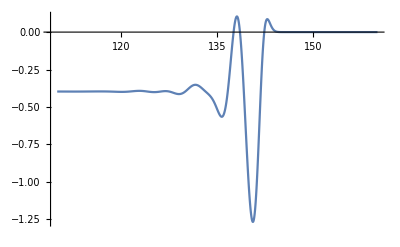

jeListsigma2v3.csv

{{110,-0.397101},{130.,-0.396711},{150.,-3.60101×10^-13}}

```mathematica
integ[start_,end_]:=lx/δk*NIntegrate[(τ-τe)*(ρσ2[τ,0]-ρ0300[τ,0]),{τ,start,end}]
oldJe=integ[110,160];
jeListσ2={{110,oldJe}};
Do[
newJe=oldJe-integ[110+i,110+i+δ];
AppendTo[jeListσ2,{(110+i+δ),newJe}];
oldJe=newJe;
Print[i];
,{i,0.,50-δ,δ}]
ListLinePlot[jeListσ2]
Export["jeListsigma2v3.csv",jeListσ2]
```

0.

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.92

0.94

0.96

0.98

1.

1.02

1.04

1.06

1.08

1.1

1.12

1.14

1.16

1.18

1.2

1.22

1.24

1.26

1.28

1.3

1.32

1.34

1.36

1.38

1.4

1.42

1.44

1.46

1.48

1.5

1.52

1.54

1.56

1.58

1.6

1.62

1.64

1.66

1.68

1.7

1.72

1.74

1.76

1.78

1.8

1.82

1.84

1.86

1.88

1.9

1.92

1.94

1.96

1.98

2.

2.02

2.04

2.06

2.08

2.1

2.12

2.14

2.16

2.18

2.2

2.22

2.24

2.26

2.28

2.3

2.32

2.34

2.36

2.38

2.4

2.42

2.44

2.46

2.48

2.5

2.52

2.54

2.56

2.58

2.6

2.62

2.64

2.66

2.68

2.7

2.72

2.74

2.76

2.78

2.8

2.82

2.84

2.86

2.88

2.9

2.92

2.94

2.96

2.98

3.

3.02

3.04

3.06

3.08

3.1

3.12

3.14

3.16

3.18

3.2

3.22

3.24

3.26

3.28

3.3

3.32

3.34

3.36

3.38

3.4

3.42

3.44

3.46

3.48

3.5

3.52

3.54

3.56

3.58

3.6

3.62

3.64

3.66

3.68

3.7

3.72

3.74

3.76

3.78

3.8

3.82

3.84

3.86

3.88

3.9

3.92

3.94

3.96

3.98

4.

4.02

4.04

4.06

4.08

4.1

4.12

4.14

4.16

4.18

4.2

4.22

4.24

4.26

4.28

4.3

4.32

4.34

4.36

4.38

4.4

4.42

4.44

4.46

4.48

4.5

4.52

4.54

4.56

4.58

4.6

4.62

4.64

4.66

4.68

4.7

4.72

4.74

4.76

4.78

4.8

4.82

4.84

4.86

4.88

4.9

4.92

4.94

4.96

4.98

5.

5.02

5.04

5.06

5.08

5.1

5.12

5.14

5.16

5.18

5.2

5.22

5.24

5.26

5.28

5.3

5.32

5.34

5.36

5.38

5.4

5.42

5.44

5.46

5.48

5.5

5.52

5.54

5.56

5.58

5.6

5.62

5.64

5.66

5.68

5.7

5.72

5.74

5.76

5.78

5.8

5.82

5.84

5.86

5.88

5.9

5.92

5.94

5.96

5.98

6.

6.02

6.04

6.06

6.08

6.1

6.12

6.14

6.16

6.18

6.2

6.22

6.24

6.26

6.28

6.3

6.32

6.34

6.36

6.38

6.4

6.42

6.44

6.46

6.48

6.5

6.52

6.54

6.56

6.58

6.6

6.62

6.64

6.66

6.68

6.7

6.72

6.74

6.76

6.78

6.8

6.82

6.84

6.86

6.88

6.9

6.92

6.94

6.96

6.98

7.

7.02

7.04

7.06

7.08

7.1

7.12

7.14

7.16

7.18

7.2

7.22

7.24

7.26

7.28

7.3

7.32

7.34

7.36

7.38

7.4

7.42

7.44

7.46

7.48

7.5

7.52

7.54

7.56

7.58

7.6

7.62

7.64

7.66

7.68

7.7

7.72

7.74

7.76

7.78

7.8

7.82

7.84

7.86

7.88

7.9

7.92

7.94

7.96

7.98

8.

8.02

8.04

8.06

8.08

8.1

8.12

8.14

8.16

8.18

8.2

8.22

8.24

8.26

8.28

8.3

8.32

8.34

8.36

8.38

8.4

8.42

8.44

8.46

8.48

8.5

8.52

8.54

8.56

8.58

8.6

8.62

8.64

8.66

8.68

8.7

8.72

8.74

8.76

8.78

8.8

8.82

8.84

8.86

8.88

8.9

8.92

8.94

8.96

8.98

9.

9.02

9.04

9.06

9.08

9.1

9.12

9.14

9.16

9.18

9.2

9.22

9.24

9.26

9.28

9.3

9.32

9.34

9.36

9.38

9.4

9.42

9.44

9.46

9.48

9.5

9.52

9.54

9.56

9.58

9.6

9.62

9.64

9.66

9.68

9.7

9.72

9.74

9.76

9.78

9.8

9.82

9.84

9.86

9.88

9.9

9.92

9.94

9.96

9.98

10.

10.02

10.04

10.06

10.08

10.1

10.12

10.14

10.16

10.18

10.2

10.22

10.24

10.26

10.28

10.3

10.32

10.34

10.36

10.38

10.4

10.42

10.44

10.46

10.48

10.5

10.52

10.54

10.56

10.58

10.6

10.62

10.64

10.66

10.68

10.7

10.72

10.74

10.76

10.78

10.8

10.82

10.84

10.86

10.88

10.9

10.92

10.94

10.96

10.98

11.

11.02

11.04

11.06

11.08

11.1

11.12

11.14

11.16

11.18

11.2

11.22

11.24

11.26

11.28

11.3

11.32

11.34

11.36

11.38

11.4

11.42

11.44

11.46

11.48

11.5

11.52

11.54

11.56

11.58

11.6

11.62

11.64

11.66

11.68

11.7

11.72

11.74

11.76

11.78

11.8

11.82

11.84

11.86

11.88

11.9

11.92

11.94

11.96

11.98

12.

12.02

12.04

12.06

12.08

12.1

12.12

12.14

12.16

12.18

12.2

12.22

12.24

12.26

12.28

12.3

12.32

12.34

12.36

12.38

12.4

12.42

12.44

12.46

12.48

12.5

12.52

12.54

12.56

12.58

12.6

12.62

12.64

12.66

12.68

12.7

12.72

12.74

12.76

12.78

12.8

12.82

12.84

12.86

12.88

12.9

12.92

12.94

12.96

12.98

13.

13.02

13.04

13.06

13.08

13.1

13.12

13.14

13.16

13.18

13.2

13.22

13.24

13.26

13.28

13.3

13.32

13.34

13.36

13.38

13.4

13.42

13.44

13.46

13.48

13.5

13.52

13.54

13.56

13.58

13.6

13.62

13.64

13.66

13.68

13.7

13.72

13.74

13.76

13.78

13.8

13.82

13.84

13.86

13.88

13.9

13.92

13.94

13.96

13.98

14.

14.02

14.04

14.06

14.08

14.1

14.12

14.14

14.16

14.18

14.2

14.22

14.24

14.26

14.28

14.3

14.32

14.34

14.36

14.38

14.4

14.42

14.44

14.46

14.48

14.5

14.52

14.54

14.56

14.58

14.6

14.62

14.64

14.66

14.68

14.7

14.72

14.74

14.76

14.78

14.8

14.82

14.84

14.86

14.88

14.9

14.92

14.94

14.96

14.98

15.

15.02

15.04

15.06

15.08

15.1

15.12

15.14

15.16

15.18

15.2

15.22

15.24

15.26

15.28

15.3

15.32

15.34

15.36

15.38

15.4

15.42

15.44

15.46

15.48

15.5

15.52

15.54

15.56

15.58

15.6

15.62

15.64

15.66

15.68

15.7

15.72

15.74

15.76

15.78

15.8

15.82

15.84

15.86

15.88

15.9

15.92

15.94

15.96

15.98

16.

16.02

16.04

16.06

16.08

16.1

16.12

16.14

16.16

16.18

16.2

16.22

16.24

16.26

16.28

16.3

16.32

16.34

16.36

16.38

16.4

16.42

16.44

16.46

16.48

16.5

16.52

16.54

16.56

16.58

16.6

16.62

16.64

16.66

16.68

16.7

16.72

16.74

16.76

16.78

16.8

16.82

16.84

16.86

16.88

16.9

16.92

16.94

16.96

16.98

17.

17.02

17.04

17.06

17.08

17.1

17.12

17.14

17.16

17.18

17.2

17.22

17.24

17.26

17.28

17.3

17.32

17.34

17.36

17.38

17.4

17.42

17.44

17.46

17.48

17.5

17.52

17.54

17.56

17.58

17.6

17.62

17.64

17.66

17.68

17.7

17.72

17.74

17.76

17.78

17.8

17.82

17.84

17.86

17.88

17.9

17.92

17.94

17.96

17.98

18.

18.02

18.04

18.06

18.08

18.1

18.12

18.14

18.16

18.18

18.2

18.22

18.24

18.26

18.28

18.3

18.32

18.34

18.36

18.38

18.4

18.42

18.44

18.46

18.48

18.5

18.52

18.54

18.56

18.58

18.6

18.62

18.64

18.66

18.68

18.7

18.72

18.74

18.76

18.78

18.8

18.82

18.84

18.86

18.88

18.9

18.92

18.94

18.96

18.98

19.

19.02

19.04

19.06

19.08

19.1

19.12

19.14

19.16

19.18

19.2

19.22

19.24

19.26

19.28

19.3

19.32

19.34

19.36

19.38

19.4

19.42

19.44

19.46

19.48

19.5

19.52

19.54

19.56

19.58

19.6

19.62

19.64

19.66

19.68

19.7

19.72

19.74

19.76

19.78

19.8

19.82

19.84

19.86

19.88

19.9

19.92

19.94

19.96

19.98

20.

20.02

20.04

20.06

20.08

20.1

20.12

20.14

20.16

20.18

20.2

20.22

20.24

20.26

20.28

20.3

20.32

20.34

20.36

20.38

20.4

20.42

20.44

20.46

20.48

20.5

20.52

20.54

20.56

20.58

20.6

20.62

20.64

20.66

20.68

20.7

20.72

20.74

20.76

20.78

20.8

20.82

20.84

20.86

20.88

20.9

20.92

20.94

20.96

20.98

21.

21.02

21.04

21.06

21.08

21.1

21.12

21.14

21.16

21.18

21.2

21.22

21.24

21.26

21.28

21.3

21.32

21.34

21.36

21.38

21.4

21.42

21.44

21.46

21.48

21.5

21.52

21.54

21.56

21.58

21.6

21.62

21.64

21.66

21.68

21.7

21.72

21.74

21.76

21.78

21.8

21.82

21.84

21.86

21.88

21.9

21.92

21.94

21.96

21.98

22.

22.02

22.04

22.06

22.08

22.1

22.12

22.14

22.16

22.18

22.2

22.22

22.24

22.26

22.28

22.3

22.32

22.34

22.36

22.38

22.4

22.42

22.44

22.46

22.48

22.5

22.52

22.54

22.56

22.58

22.6

22.62

22.64

22.66

22.68

22.7

22.72

22.74

22.76

22.78

22.8

22.82

22.84

22.86

22.88

22.9

22.92

22.94

22.96

22.98

23.

23.02

23.04

23.06

23.08

23.1

23.12

23.14

23.16

23.18

23.2

23.22

23.24

23.26

23.28

23.3

23.32

23.34

23.36

23.38

23.4

23.42

23.44

23.46

23.48

23.5

23.52

23.54

23.56

23.58

23.6

23.62

23.64

23.66

23.68

23.7

23.72

23.74

23.76

23.78

23.8

23.82

23.84

23.86

23.88

23.9

23.92

23.94

23.96

23.98

24.

24.02

24.04

24.06

24.08

24.1

24.12

24.14

24.16

24.18

24.2

24.22

24.24

24.26

24.28

24.3

24.32

24.34

24.36

24.38

24.4

24.42

24.44

24.46

24.48

24.5

24.52

24.54

24.56

24.58

24.6

24.62

24.64

24.66

24.68

24.7

24.72

24.74

24.76

24.78

24.8

24.82

24.84

24.86

24.88

24.9

24.92

24.94

24.96

24.98

25.

25.02

25.04

25.06

25.08

25.1

25.12

25.14

25.16

25.18

25.2

25.22

25.24

25.26

25.28

25.3

25.32

25.34

25.36

25.38

25.4

25.42

25.44

25.46

25.48

25.5

25.52

25.54

25.56

25.58

25.6

25.62

25.64

25.66

25.68

25.7

25.72

25.74

25.76

25.78

25.8

25.82

25.84

25.86

25.88

25.9

25.92

25.94

25.96

25.98

26.

26.02

26.04

26.06

26.08

26.1

26.12

26.14

26.16

26.18

26.2

26.22

26.24

26.26

26.28

26.3

26.32

26.34

26.36

26.38

26.4

26.42

26.44

26.46

26.48

26.5

26.52

26.54

26.56

26.58

26.6

26.62

26.64

26.66

26.68

26.7

26.72

26.74

26.76

26.78

26.8

26.82

26.84

26.86

26.88

26.9

26.92

26.94

26.96

26.98

27.

27.02

27.04

27.06

27.08

27.1

27.12

27.14

27.16

27.18

27.2

27.22

27.24

27.26

27.28

27.3

27.32

27.34

27.36

27.38

27.4

27.42

27.44

27.46

27.48

27.5

27.52

27.54

27.56

27.58

27.6

27.62

27.64

27.66

27.68

27.7

27.72

27.74

27.76

27.78

27.8

27.82

27.84

27.86

27.88

27.9

27.92

27.94

27.96

27.98

28.

28.02

28.04

28.06

28.08

28.1

28.12

28.14

28.16

28.18

28.2

28.22

28.24

28.26

28.28

28.3

28.32

28.34

28.36

28.38

28.4

28.42

28.44

28.46

28.48

28.5

28.52

28.54

28.56

28.58

28.6

28.62

28.64

28.66

28.68

28.7

28.72

28.74

28.76

28.78

28.8

28.82

28.84

28.86

28.88

28.9

28.92

28.94

28.96

28.98

29.

29.02

29.04

29.06

29.08

29.1

29.12

29.14

29.16

29.18

29.2

29.22

29.24

29.26

29.28

29.3

29.32

29.34

29.36

29.38

29.4

29.42

29.44

29.46

29.48

29.5

29.52

29.54

29.56

29.58

29.6

29.62

29.64

29.66

29.68

29.7

29.72

29.74

29.76

29.78

29.8

29.82

29.84

29.86

29.88

29.9

29.92

29.94

29.96

29.98

30.

30.02

30.04

30.06

30.08

30.1

30.12

30.14

30.16

30.18

30.2

30.22

30.24

30.26

30.28

30.3

30.32

30.34

30.36

30.38

30.4

30.42

30.44

30.46

30.48

30.5

30.52

30.54

30.56

30.58

30.6

30.62

30.64

30.66

30.68

30.7

30.72

30.74

30.76

30.78

30.8

30.82

30.84

30.86

30.88

30.9

30.92

30.94

30.96

30.98

31.

31.02

31.04

31.06

31.08

31.1

31.12

31.14

31.16

31.18

31.2

31.22

31.24

31.26

31.28

31.3

31.32

31.34

31.36

31.38

31.4

31.42

31.44

31.46

31.48

31.5

31.52

31.54

31.56

31.58

31.6

31.62

31.64

31.66

31.68

31.7

31.72

31.74

31.76

31.78

31.8

31.82

31.84

31.86

31.88

31.9

31.92

31.94

31.96

31.98

32.

32.02

32.04

32.06

32.08

32.1

32.12

32.14

32.16

32.18

32.2

32.22

32.24

32.26

32.28

32.3

32.32

32.34

32.36

32.38

32.4

32.42

32.44

32.46

32.48

32.5

32.52

32.54

32.56

32.58

32.6

32.62

32.64

32.66

32.68

32.7

32.72

32.74

32.76

32.78

32.8

32.82

32.84

32.86

32.88

32.9

32.92

32.94

32.96

32.98

33.

33.02

33.04

33.06

33.08

33.1

33.12

33.14

33.16

33.18

33.2

33.22

33.24

33.26

33.28

33.3

33.32

33.34

33.36

33.38

33.4

33.42

33.44

33.46

33.48

33.5

33.52

33.54

33.56

33.58

33.6

33.62

33.64

33.66

33.68

33.7

33.72

33.74

33.76

33.78

33.8

33.82

33.84

33.86

33.88

33.9

33.92

33.94

33.96

33.98

34.

34.02

34.04

34.06

34.08

34.1

34.12

34.14

34.16

34.18

34.2

34.22

34.24

34.26

34.28

34.3

34.32

34.34

34.36

34.38

34.4

34.42

34.44

34.46

34.48

34.5

34.52

34.54

34.56

34.58

34.6

34.62

34.64

34.66

34.68

34.7

34.72

34.74

34.76

34.78

34.8

34.82

34.84

34.86

34.88

34.9

34.92

34.94

34.96

34.98

35.

35.02

35.04

35.06

35.08

35.1

35.12

35.14

35.16

35.18

35.2

35.22

35.24

35.26

35.28

35.3

35.32

35.34

35.36

35.38

35.4

35.42

35.44

35.46

35.48

35.5

35.52

35.54

35.56

35.58

35.6

35.62

35.64

35.66

35.68

35.7

35.72

35.74

35.76

35.78

35.8

35.82

35.84

35.86

35.88

35.9

35.92

35.94

35.96

35.98

36.

36.02

36.04

36.06

36.08

36.1

36.12

36.14

36.16

36.18

36.2

36.22

36.24

36.26

36.28

36.3

36.32

36.34

36.36

36.38

36.4

36.42

36.44

36.46

36.48

36.5

36.52

36.54

36.56

36.58

36.6

36.62

36.64

36.66

36.68

36.7

36.72

36.74

36.76

36.78

36.8

36.82

36.84

36.86

36.88

36.9

36.92

36.94

36.96

36.98

37.

37.02

37.04

37.06

37.08

37.1

37.12

37.14

37.16

37.18

37.2

37.22

37.24

37.26

37.28

37.3

37.32

37.34

37.36

37.38

37.4

37.42

37.44

37.46

37.48

37.5

37.52

37.54

37.56

37.58

37.6

37.62

37.64

37.66

37.68

37.7

37.72

37.74

37.76

37.78

37.8

37.82

37.84

37.86

37.88

37.9

37.92

37.94

37.96

37.98

38.

38.02

38.04

38.06

38.08

38.1

38.12

38.14

38.16

38.18

38.2

38.22

38.24

38.26

38.28

38.3

38.32

38.34

38.36

38.38

38.4

38.42

38.44

38.46

38.48

38.5

38.52

38.54

38.56

38.58

38.6

38.62

38.64

38.66

38.68

38.7

38.72

38.74

38.76

38.78

38.8

38.82

38.84

38.86

38.88

38.9

38.92

38.94

38.96

38.98

39.

39.02

39.04

39.06

39.08

39.1

39.12

39.14

39.16

39.18

39.2

39.22

39.24

39.26

39.28

39.3

39.32

39.34

39.36

39.38

39.4

39.42

39.44

39.46

39.48

39.5

39.52

39.54

39.56

39.58

39.6

39.62

39.64

39.66

39.68

39.7

39.72

39.74

39.76

39.78

39.8

39.82

39.84

39.86

39.88

39.9

39.92

39.94

39.96

39.98

40.

40.02

40.04

40.06

40.08

40.1

40.12

40.14

40.16

40.18

40.2

40.22

40.24

40.26

40.28

40.3

40.32

40.34

40.36

40.38

40.4

40.42

40.44

40.46

40.48

40.5

40.52

40.54

40.56

40.58

40.6

40.62

40.64

40.66

40.68

40.7

40.72

40.74

40.76

40.78

40.8

40.82

40.84

40.86

40.88

40.9

40.92

40.94

40.96

40.98

41.

41.02

41.04

41.06

41.08

41.1

41.12

41.14

41.16

41.18

41.2

41.22

41.24

41.26

41.28

41.3

41.32

41.34

41.36

41.38

41.4

41.42

41.44

41.46

41.48

41.5

41.52

41.54

41.56

41.58

41.6

41.62

41.64

41.66

41.68

41.7

41.72

41.74

41.76

41.78

41.8

41.82

41.84

41.86

41.88

41.9

41.92

41.94

41.96

41.98

42.

42.02

42.04

42.06

42.08

42.1

42.12

42.14

42.16

42.18

42.2

42.22

42.24

42.26

42.28

42.3

42.32

42.34

42.36

42.38

42.4

42.42

42.44

42.46

42.48

42.5

42.52

42.54

42.56

42.58

42.6

42.62

42.64

42.66

42.68

42.7

42.72

42.74

42.76

42.78

42.8

42.82

42.84

42.86

42.88

42.9

42.92

42.94

42.96

42.98

43.

43.02

43.04

43.06

43.08

43.1

43.12

43.14

43.16

43.18

43.2

43.22

43.24

43.26

43.28

43.3

43.32

43.34

43.36

43.38

43.4

43.42

43.44

43.46

43.48

43.5

43.52

43.54

43.56

43.58

43.6

43.62

43.64

43.66

43.68

43.7

43.72

43.74

43.76

43.78

43.8

43.82

43.84

43.86

43.88

43.9

43.92

43.94

43.96

43.98

44.

44.02

44.04

44.06

44.08

44.1

44.12

44.14

44.16

44.18

44.2

44.22

44.24

44.26

44.28

44.3

44.32

44.34

44.36

44.38

44.4

44.42

44.44

44.46

44.48

44.5

44.52

44.54

44.56

44.58

44.6

44.62

44.64

44.66

44.68

44.7

44.72

44.74

44.76

44.78

44.8

44.82

44.84

44.86

44.88

44.9

44.92

44.94

44.96

44.98

45.

45.02

45.04

45.06

45.08

45.1

45.12

45.14

45.16

45.18

45.2

45.22

45.24

45.26

45.28

45.3

45.32

45.34

45.36

45.38

45.4

45.42

45.44

45.46

45.48

45.5

45.52

45.54

45.56

45.58

45.6

45.62

45.64

45.66

45.68

45.7

45.72

45.74

45.76

45.78

45.8

45.82

45.84

45.86

45.88

45.9

45.92

45.94

45.96

45.98

46.

46.02

46.04

46.06

46.08

46.1

46.12

46.14

46.16

46.18

46.2

46.22

46.24

46.26

46.28

46.3

46.32

46.34

46.36

46.38

46.4

46.42

46.44

46.46

46.48

46.5

46.52

46.54

46.56

46.58

46.6

46.62

46.64

46.66

46.68

46.7

46.72

46.74

46.76

46.78

46.8

46.82

46.84

46.86

46.88

46.9

46.92

46.94

46.96

46.98

47.

47.02

47.04

47.06

47.08

47.1

47.12

47.14

47.16

47.18

47.2

47.22

47.24

47.26

47.28

47.3

47.32

47.34

47.36

47.38

47.4

47.42

47.44

47.46

47.48

47.5

47.52

47.54

47.56

47.58

47.6

47.62

47.64

47.66

47.68

47.7

47.72

47.74

47.76

47.78

47.8

47.82

47.84

47.86

47.88

47.9

47.92

47.94

47.96

47.98

48.

48.02

48.04

48.06

48.08

48.1

48.12

48.14

48.16

48.18

48.2

48.22

48.24

48.26

48.28

48.3

48.32

48.34

48.36

48.38

48.4

48.42

48.44

48.46

48.48

48.5

48.52

48.54

48.56

48.58

48.6

48.62

48.64

48.66

48.68

48.7

48.72

48.74

48.76

48.78

48.8

48.82

48.84

48.86

48.88

48.9

48.92

48.94

48.96

48.98

49.

49.02

49.04

49.06

49.08

49.1

49.12

49.14

49.16

49.18

49.2

49.22

49.24

49.26

49.28

49.3

49.32

49.34

49.36

49.38

49.4

49.42

49.44

49.46

49.48

49.5

49.52

49.54

49.56

49.58

49.6

49.62

49.64

49.66

49.68

49.7

49.72

49.74

49.76

49.78

49.8

49.82

49.84

49.86

49.88

49.9

49.92

49.94

49.96

49.98

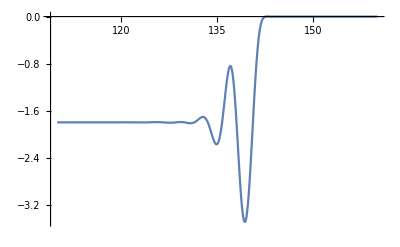

jeListpsi1v3.csv

{{110,-1.8},{130.,-1.80224},{150.,-2.77933×10^-12}}

```mathematica
integ[start_,end_]:=lx/δk*NIntegrate[(τ-τe)*(ρψ1[τ,0]-ρ0299[τ,0]),{τ,start,end}]
oldJe=integ[110,160];
jeListψ1={{110,oldJe}};
Do[
newJe=oldJe-integ[110+i,110+i+δ];
AppendTo[jeListψ1,{(110+i+δ),newJe}];
oldJe=newJe;
Print[i];
,{i,0.,50-δ,δ}]
ListLinePlot[jeListψ1]
Export["jeListpsi1v3.csv",jeListψ1]
(*Export["jeListpsi1modv3.csv",jeListψ1New]*)
```

0.

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.92

0.94

0.96

0.98

1.

1.02

1.04

1.06

1.08

1.1

1.12

1.14

1.16

1.18

1.2

1.22

1.24

1.26

1.28

1.3

1.32

1.34

1.36

1.38

1.4

1.42

1.44

1.46

1.48

1.5

1.52

1.54

1.56

1.58

1.6

1.62

1.64

1.66

1.68

1.7

1.72

1.74

1.76

1.78

1.8

1.82

1.84

1.86

1.88

1.9

1.92

1.94

1.96

1.98

2.

2.02

2.04

2.06

2.08

2.1

2.12

2.14

2.16

2.18

2.2

2.22

2.24

2.26

2.28

2.3

2.32

2.34

2.36

2.38

2.4

2.42

2.44

2.46

2.48

2.5

2.52

2.54

2.56

2.58

2.6

2.62

2.64

2.66

2.68

2.7

2.72

2.74

2.76

2.78

2.8

2.82

2.84

2.86

2.88

2.9

2.92

2.94

2.96

2.98

3.

3.02

3.04

3.06

3.08

3.1

3.12

3.14

3.16

3.18

3.2

3.22

3.24

3.26

3.28

3.3

3.32

3.34

3.36

3.38

3.4

3.42

3.44

3.46

3.48

3.5

3.52

3.54

3.56

3.58

3.6

3.62

3.64

3.66

3.68

3.7

3.72

3.74

3.76

3.78

3.8

3.82

3.84

3.86

3.88

3.9

3.92

3.94

3.96

3.98

4.

4.02

4.04

4.06

4.08

4.1

4.12

4.14

4.16

4.18

4.2

4.22

4.24

4.26

4.28

4.3

4.32

4.34

4.36

4.38

4.4

4.42

4.44

4.46

4.48

4.5

4.52

4.54

4.56

4.58

4.6

4.62

4.64

4.66

4.68

4.7

4.72

4.74

4.76

4.78

4.8

4.82

4.84

4.86

4.88

4.9

4.92

4.94

4.96

4.98

5.

5.02

5.04

5.06

5.08

5.1

5.12

5.14

5.16

5.18

5.2

5.22

5.24

5.26

5.28

5.3

5.32

5.34

5.36

5.38

5.4

5.42

5.44

5.46

5.48

5.5

5.52

5.54

5.56

5.58

5.6

5.62

5.64

5.66

5.68

5.7

5.72

5.74

5.76

5.78

5.8

5.82

5.84

5.86

5.88

5.9

5.92

5.94

5.96

5.98

6.

6.02

6.04

6.06

6.08

6.1

6.12

6.14

6.16

6.18

6.2

6.22

6.24

6.26

6.28

6.3

6.32

6.34

6.36

6.38

6.4

6.42

6.44

6.46

6.48

6.5

6.52

6.54

6.56

6.58

6.6

6.62

6.64

6.66

6.68

6.7

6.72

6.74

6.76

6.78

6.8

6.82

6.84

6.86

6.88

6.9

6.92

6.94

6.96

6.98

7.

7.02

7.04

7.06

7.08

7.1

7.12

7.14

7.16

7.18

7.2

7.22

7.24

7.26

7.28

7.3

7.32

7.34

7.36

7.38

7.4

7.42

7.44

7.46

7.48

7.5

7.52

7.54

7.56

7.58

7.6

7.62

7.64

7.66

7.68

7.7

7.72

7.74

7.76

7.78

7.8

7.82

7.84

7.86

7.88

7.9

7.92

7.94

7.96

7.98

8.

8.02

8.04

8.06

8.08

8.1

8.12

8.14

8.16

8.18

8.2

8.22

8.24

8.26

8.28

8.3

8.32

8.34

8.36

8.38

8.4

8.42

8.44

8.46

8.48

8.5

8.52

8.54

8.56

8.58

8.6

8.62

8.64

8.66

8.68

8.7

8.72

8.74

8.76

8.78

8.8

8.82

8.84

8.86

8.88

8.9

8.92

8.94

8.96

8.98

9.

9.02

9.04

9.06

9.08

9.1

9.12

9.14

9.16

9.18

9.2

9.22

9.24

9.26

9.28

9.3

9.32

9.34

9.36

9.38

9.4

9.42

9.44

9.46

9.48

9.5

9.52

9.54

9.56

9.58

9.6

9.62

9.64

9.66

9.68

9.7

9.72

9.74

9.76

9.78

9.8

9.82

9.84

9.86

9.88

9.9

9.92

9.94

9.96

9.98

10.

10.02

10.04

10.06

10.08

10.1

10.12

10.14

10.16

10.18

10.2

10.22

10.24

10.26

10.28

10.3

10.32

10.34

10.36

10.38

10.4

10.42

10.44

10.46

10.48

10.5

10.52

10.54

10.56

10.58

10.6

10.62

10.64

10.66

10.68

10.7

10.72

10.74

10.76

10.78

10.8

10.82

10.84

10.86

10.88

10.9

10.92

10.94

10.96

10.98

11.

11.02

11.04

11.06

11.08

11.1

11.12

11.14

11.16

11.18

11.2

11.22

11.24

11.26

11.28

11.3

11.32

11.34

11.36

11.38

11.4

11.42

11.44

11.46

11.48

11.5

11.52

11.54

11.56

11.58

11.6

11.62

11.64

11.66

11.68

11.7

11.72

11.74

11.76

11.78

11.8

11.82

11.84

11.86

11.88

11.9

11.92

11.94

11.96

11.98

12.

12.02

12.04

12.06

12.08

12.1

12.12

12.14

12.16

12.18

12.2

12.22

12.24

12.26

12.28

12.3

12.32

12.34

12.36

12.38

12.4

12.42

12.44

12.46

12.48

12.5

12.52

12.54

12.56

12.58

12.6

12.62

12.64

12.66

12.68

12.7

12.72

12.74

12.76

12.78

12.8

12.82

12.84

12.86

12.88

12.9

12.92

12.94

12.96

12.98

13.

13.02

13.04

13.06

13.08

13.1

13.12

13.14

13.16

13.18

13.2

13.22

13.24

13.26

13.28

13.3

13.32

13.34

13.36

13.38

13.4

13.42

13.44

13.46

13.48

13.5

13.52

13.54

13.56

13.58

13.6

13.62

13.64

13.66

13.68

13.7

13.72

13.74

13.76

13.78

13.8

13.82

13.84

13.86

13.88

13.9

13.92

13.94

13.96

13.98

14.

14.02

14.04

14.06

14.08

14.1

14.12

14.14

14.16

14.18

14.2

14.22

14.24

14.26

14.28

14.3

14.32

14.34

14.36

14.38

14.4

14.42

14.44

14.46

14.48

14.5

14.52

14.54

14.56

14.58

14.6

14.62

14.64

14.66

14.68

14.7

14.72

14.74

14.76

14.78

14.8

14.82

14.84

14.86

14.88

14.9

14.92

14.94

14.96

14.98

15.

15.02

15.04

15.06

15.08

15.1

15.12

15.14

15.16

15.18

15.2

15.22

15.24

15.26

15.28

15.3

15.32

15.34

15.36

15.38

15.4

15.42

15.44

15.46

15.48

15.5

15.52

15.54

15.56

15.58

15.6

15.62

15.64

15.66

15.68

15.7

15.72

15.74

15.76

15.78

15.8

15.82

15.84

15.86

15.88

15.9

15.92

15.94

15.96

15.98

16.

16.02

16.04

16.06

16.08

16.1

16.12

16.14

16.16

16.18

16.2

16.22

16.24

16.26

16.28

16.3

16.32

16.34

16.36

16.38

16.4

16.42

16.44

16.46

16.48

16.5

16.52

16.54

16.56

16.58

16.6

16.62

16.64

16.66

16.68

16.7

16.72

16.74

16.76

16.78

16.8

16.82

16.84

16.86

16.88

16.9

16.92

16.94

16.96

16.98

17.

17.02

17.04

17.06

17.08

17.1

17.12

17.14

17.16

17.18

17.2

17.22

17.24

17.26

17.28

17.3

17.32

17.34

17.36

17.38

17.4

17.42

17.44

17.46

17.48

17.5

17.52

17.54

17.56

17.58

17.6

17.62

17.64

17.66

17.68

17.7

17.72

17.74

17.76

17.78

17.8

17.82

17.84

17.86

17.88

17.9

17.92

17.94

17.96

17.98

18.

18.02

18.04

18.06

18.08

18.1

18.12

18.14

18.16

18.18

18.2

18.22

18.24

18.26

18.28

18.3

18.32

18.34

18.36

18.38

18.4

18.42

18.44

18.46

18.48

18.5

18.52

18.54

18.56

18.58

18.6

18.62

18.64

18.66

18.68

18.7

18.72

18.74

18.76

18.78

18.8

18.82

18.84

18.86

18.88

18.9

18.92

18.94

18.96

18.98

19.

19.02

19.04

19.06

19.08

19.1

19.12

19.14

19.16

19.18

19.2

19.22

19.24

19.26

19.28

19.3

19.32

19.34

19.36

19.38

19.4

19.42

19.44

19.46

19.48

19.5

19.52

19.54

19.56

19.58

19.6

19.62

19.64

19.66

19.68

19.7

19.72

19.74

19.76

19.78

19.8

19.82

19.84

19.86

19.88

19.9

19.92

19.94

19.96

19.98

20.

20.02

20.04

20.06

20.08

20.1

20.12

20.14

20.16

20.18

20.2

20.22

20.24

20.26

20.28

20.3

20.32

20.34

20.36

20.38

20.4

20.42

20.44

20.46

20.48

20.5

20.52

20.54

20.56

20.58

20.6

20.62

20.64

20.66

20.68

20.7

20.72

20.74

20.76

20.78

20.8

20.82

20.84

20.86

20.88

20.9

20.92

20.94

20.96

20.98

21.

21.02

21.04

21.06

21.08

21.1

21.12

21.14

21.16

21.18

21.2

21.22

21.24

21.26

21.28

21.3

21.32

21.34

21.36

21.38

21.4

21.42

21.44

21.46

21.48

21.5

21.52

21.54

21.56

21.58

21.6

21.62

21.64

21.66

21.68

21.7

21.72

21.74

21.76

21.78

21.8

21.82

21.84

21.86

21.88

21.9

21.92

21.94

21.96

21.98

22.

22.02

22.04

22.06

22.08

22.1

22.12

22.14

22.16

22.18

22.2

22.22

22.24

22.26

22.28

22.3

22.32

22.34

22.36

22.38

22.4

22.42

22.44

22.46

22.48

22.5

22.52

22.54

22.56

22.58

22.6

22.62

22.64

22.66

22.68

22.7

22.72

22.74

22.76

22.78

22.8

22.82

22.84

22.86

22.88

22.9

22.92

22.94

22.96

22.98

23.

23.02

23.04

23.06

23.08

23.1

23.12

23.14

23.16

23.18

23.2

23.22

23.24

23.26

23.28

23.3

23.32

23.34

23.36

23.38

23.4

23.42

23.44

23.46

23.48

23.5

23.52

23.54

23.56

23.58

23.6

23.62

23.64

23.66

23.68

23.7

23.72

23.74

23.76

23.78

23.8

23.82

23.84

23.86

23.88

23.9

23.92

23.94

23.96

23.98

24.

24.02

24.04

24.06

24.08

24.1

24.12

24.14

24.16

24.18

24.2

24.22

24.24

24.26

24.28

24.3

24.32

24.34

24.36

24.38

24.4

24.42

24.44

24.46

24.48

24.5

24.52

24.54

24.56

24.58

24.6

24.62

24.64

24.66

24.68

24.7

24.72

24.74

24.76

24.78

24.8

24.82

24.84

24.86

24.88

24.9

24.92

24.94

24.96

24.98

25.

25.02

25.04

25.06

25.08

25.1

25.12

25.14

25.16

25.18

25.2

25.22

25.24

25.26

25.28

25.3

25.32

25.34

25.36

25.38

25.4

25.42

25.44

25.46

25.48

25.5

25.52

25.54

25.56

25.58

25.6

25.62

25.64

25.66

25.68

25.7

25.72

25.74

25.76

25.78

25.8

25.82

25.84

25.86

25.88

25.9

25.92

25.94

25.96

25.98

26.

26.02

26.04

26.06

26.08

26.1

26.12

26.14

26.16

26.18

26.2

26.22

26.24

26.26

26.28

26.3

26.32

26.34

26.36

26.38

26.4

26.42

26.44

26.46

26.48

26.5

26.52

26.54

26.56

26.58

26.6

26.62

26.64

26.66

26.68

26.7

26.72

26.74

26.76

26.78

26.8

26.82

26.84

26.86

26.88

26.9

26.92

26.94

26.96

26.98

27.

27.02

27.04

27.06

27.08

27.1

27.12

27.14

27.16

27.18

27.2

27.22

27.24

27.26

27.28

27.3

27.32

27.34

27.36

27.38

27.4

27.42

27.44

27.46

27.48

27.5

27.52

27.54

27.56

27.58

27.6

27.62

27.64

27.66

27.68

27.7

27.72

27.74

27.76

27.78

27.8

27.82

27.84

27.86

27.88

27.9

27.92

27.94

27.96

27.98

28.

28.02

28.04

28.06

28.08

28.1

28.12

28.14

28.16

28.18

28.2

28.22

28.24

28.26

28.28

28.3

28.32

28.34

28.36

28.38

28.4

28.42

28.44

28.46

28.48

28.5

28.52

28.54

28.56

28.58

28.6

28.62

28.64

28.66

28.68

28.7

28.72

28.74

28.76

28.78

28.8

28.82

28.84

28.86

28.88

28.9

28.92

28.94

28.96

28.98

29.

29.02

29.04

29.06

29.08

29.1

29.12

29.14

29.16

29.18

29.2

29.22

29.24

29.26

29.28

29.3

29.32

29.34

29.36

29.38

29.4

29.42

29.44

29.46

29.48

29.5

29.52

29.54

29.56

29.58

29.6

29.62

29.64

29.66

29.68

29.7

29.72

29.74

29.76

29.78

29.8

29.82

29.84

29.86

29.88

29.9

29.92

29.94

29.96

29.98

30.

30.02

30.04

30.06

30.08

30.1

30.12

30.14

30.16

30.18

30.2

30.22

30.24

30.26

30.28

30.3

30.32

30.34

30.36

30.38

30.4

30.42

30.44

30.46

30.48

30.5

30.52

30.54

30.56

30.58

30.6

30.62

30.64

30.66

30.68

30.7

30.72

30.74

30.76

30.78

30.8

30.82

30.84

30.86

30.88

30.9

30.92

30.94

30.96

30.98

31.

31.02

31.04

31.06

31.08

31.1

31.12

31.14

31.16

31.18

31.2

31.22

31.24

31.26

31.28

31.3

31.32

31.34

31.36

31.38

31.4

31.42

31.44

31.46

31.48

31.5

31.52

31.54

31.56

31.58

31.6

31.62

31.64

31.66

31.68

31.7

31.72

31.74

31.76

31.78

31.8

31.82

31.84

31.86

31.88

31.9

31.92

31.94

31.96

31.98

32.

32.02

32.04

32.06

32.08

32.1

32.12

32.14

32.16

32.18

32.2

32.22

32.24

32.26

32.28

32.3

32.32

32.34

32.36

32.38

32.4

32.42

32.44

32.46

32.48

32.5

32.52

32.54

32.56

32.58

32.6

32.62

32.64

32.66

32.68

32.7

32.72

32.74

32.76

32.78

32.8

32.82

32.84

32.86

32.88

32.9

32.92

32.94

32.96

32.98

33.

33.02

33.04

33.06

33.08

33.1

33.12

33.14

33.16

33.18

33.2

33.22

33.24

33.26

33.28

33.3

33.32

33.34

33.36

33.38

33.4

33.42

33.44

33.46

33.48

33.5

33.52

33.54

33.56

33.58

33.6

33.62

33.64

33.66

33.68

33.7

33.72

33.74

33.76

33.78

33.8

33.82

33.84

33.86

33.88

33.9

33.92

33.94

33.96

33.98

34.

34.02

34.04

34.06

34.08

34.1

34.12

34.14

34.16

34.18

34.2

34.22

34.24

34.26

34.28

34.3

34.32

34.34

34.36

34.38

34.4

34.42

34.44

34.46

34.48

34.5

34.52

34.54

34.56

34.58

34.6

34.62

34.64

34.66

34.68

34.7

34.72

34.74

34.76

34.78

34.8

34.82

34.84

34.86

34.88

34.9

34.92

34.94

34.96

34.98

35.

35.02

35.04

35.06

35.08

35.1

35.12

35.14

35.16

35.18

35.2

35.22

35.24

35.26

35.28

35.3

35.32

35.34

35.36

35.38

35.4

35.42

35.44

35.46

35.48

35.5

35.52

35.54

35.56

35.58

35.6

35.62

35.64

35.66

35.68

35.7

35.72

35.74

35.76

35.78

35.8

35.82

35.84

35.86

35.88

35.9

35.92

35.94

35.96

35.98

36.

36.02

36.04

36.06

36.08

36.1

36.12

36.14

36.16

36.18

36.2

36.22

36.24

36.26

36.28

36.3

36.32

36.34

36.36

36.38

36.4

36.42

36.44

36.46

36.48

36.5

36.52

36.54

36.56

36.58

36.6

36.62

36.64

36.66

36.68

36.7

36.72

36.74

36.76

36.78

36.8

36.82

36.84

36.86

36.88

36.9

36.92

36.94

36.96

36.98

37.

37.02

37.04

37.06

37.08

37.1

37.12

37.14

37.16

37.18

37.2

37.22

37.24

37.26

37.28

37.3

37.32

37.34

37.36

37.38

37.4

37.42

37.44

37.46

37.48

37.5

37.52

37.54

37.56

37.58

37.6

37.62

37.64

37.66

37.68

37.7

37.72

37.74

37.76

37.78

37.8

37.82

37.84

37.86

37.88

37.9

37.92

37.94

37.96

37.98

38.

38.02

38.04

38.06

38.08

38.1

38.12

38.14

38.16

38.18

38.2

38.22

38.24

38.26

38.28

38.3

38.32

38.34

38.36

38.38

38.4

38.42

38.44

38.46

38.48

38.5

38.52

38.54

38.56

38.58

38.6

38.62

38.64

38.66

38.68

38.7

38.72

38.74

38.76

38.78

38.8

38.82

38.84

38.86

38.88

38.9

38.92

38.94

38.96

38.98

39.

39.02

39.04

39.06

39.08

39.1

39.12

39.14

39.16

39.18

39.2

39.22

39.24

39.26

39.28

39.3

39.32

39.34

39.36

39.38

39.4

39.42

39.44

39.46

39.48

39.5

39.52

39.54

39.56

39.58

39.6

39.62

39.64

39.66

39.68

39.7

39.72

39.74

39.76

39.78

39.8

39.82

39.84

39.86

39.88

39.9

39.92

39.94

39.96

39.98

40.

40.02

40.04

40.06

40.08

40.1

40.12

40.14

40.16

40.18

40.2

40.22

40.24

40.26

40.28

40.3

40.32

40.34

40.36

40.38

40.4

40.42

40.44

40.46

40.48

40.5

40.52

40.54

40.56

40.58

40.6

40.62

40.64

40.66

40.68

40.7

40.72

40.74

40.76

40.78

40.8

40.82

40.84

40.86

40.88

40.9

40.92

40.94

40.96

40.98

41.

41.02

41.04

41.06

41.08

41.1

41.12

41.14

41.16

41.18

41.2

41.22

41.24

41.26

41.28

41.3

41.32

41.34

41.36

41.38

41.4

41.42

41.44

41.46

41.48

41.5

41.52

41.54

41.56

41.58

41.6

41.62

41.64

41.66

41.68

41.7

41.72

41.74

41.76

41.78

41.8

41.82

41.84

41.86

41.88

41.9

41.92

41.94

41.96

41.98

42.

42.02

42.04

42.06

42.08

42.1

42.12

42.14

42.16

42.18

42.2

42.22

42.24

42.26

42.28

42.3

42.32

42.34

42.36

42.38

42.4

42.42

42.44

42.46

42.48

42.5

42.52

42.54

42.56

42.58

42.6

42.62

42.64

42.66

42.68

42.7

42.72

42.74

42.76

42.78

42.8

42.82

42.84

42.86

42.88

42.9

42.92

42.94

42.96

42.98

43.

43.02

43.04

43.06

43.08

43.1

43.12

43.14

43.16

43.18

43.2

43.22

43.24

43.26

43.28

43.3

43.32

43.34

43.36

43.38

43.4

43.42

43.44

43.46

43.48

43.5

43.52

43.54

43.56

43.58

43.6

43.62

43.64

43.66

43.68

43.7

43.72

43.74

43.76

43.78

43.8

43.82

43.84

43.86

43.88

43.9

43.92

43.94

43.96

43.98

44.

44.02

44.04

44.06

44.08

44.1

44.12

44.14

44.16

44.18

44.2

44.22

44.24

44.26

44.28

44.3

44.32

44.34

44.36

44.38

44.4

44.42

44.44

44.46

44.48

44.5

44.52

44.54

44.56

44.58

44.6

44.62

44.64

44.66

44.68

44.7

44.72

44.74

44.76

44.78

44.8

44.82

44.84

44.86

44.88

44.9

44.92

44.94

44.96

44.98

45.

45.02

45.04

45.06

45.08

45.1

45.12

45.14

45.16

45.18

45.2

45.22

45.24

45.26

45.28

45.3

45.32

45.34

45.36

45.38

45.4

45.42

45.44

45.46

45.48

45.5

45.52

45.54

45.56

45.58

45.6

45.62

45.64

45.66

45.68

45.7

45.72

45.74

45.76

45.78

45.8

45.82

45.84

45.86

45.88

45.9

45.92

45.94

45.96

45.98

46.

46.02

46.04

46.06

46.08

46.1

46.12

46.14

46.16

46.18

46.2

46.22

46.24

46.26

46.28

46.3

46.32

46.34

46.36

46.38

46.4

46.42

46.44

46.46

46.48

46.5

46.52

46.54

46.56

46.58

46.6

46.62

46.64

46.66

46.68

46.7

46.72

46.74

46.76

46.78

46.8

46.82

46.84

46.86

46.88

46.9

46.92

46.94

46.96

46.98

47.

47.02

47.04

47.06

47.08

47.1

47.12

47.14

47.16

47.18

47.2

47.22

47.24

47.26

47.28

47.3

47.32

47.34

47.36

47.38

47.4

47.42

47.44

47.46

47.48

47.5

47.52

47.54

47.56

47.58

47.6

47.62

47.64

47.66

47.68

47.7

47.72

47.74

47.76

47.78

47.8

47.82

47.84

47.86

47.88

47.9

47.92

47.94

47.96

47.98

48.

48.02

48.04

48.06

48.08

48.1

48.12

48.14

48.16

48.18

48.2

48.22

48.24

48.26

48.28

48.3

48.32

48.34

48.36

48.38

48.4

48.42

48.44

48.46

48.48

48.5

48.52

48.54

48.56

48.58

48.6

48.62

48.64

48.66

48.68

48.7

48.72

48.74

48.76

48.78

48.8

48.82

48.84

48.86

48.88

48.9

48.92

48.94

48.96

48.98

49.

49.02

49.04

49.06

49.08

49.1

49.12

49.14

49.16

49.18

49.2

49.22

49.24

49.26

49.28

49.3

49.32

49.34

49.36

49.38

49.4

49.42

49.44

49.46

49.48

49.5

49.52

49.54

49.56

49.58

49.6

49.62

49.64

49.66

49.68

49.7

49.72

49.74

49.76

49.78

49.8

49.82

49.84

49.86

49.88

49.9

49.92

49.94

49.96

49.98

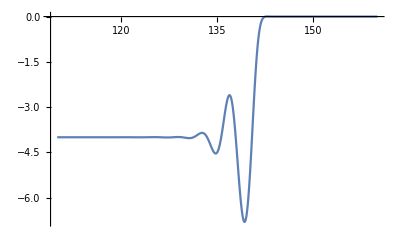

jeListpsi2v3.csv

{{110,-4.},{130.,-4.01569},{150.,-1.02762×10^-12}}

```mathematica
integ[start_,end_]:=lx/δk*NIntegrate[(τ-τe)*(ρψ2[τ,0]-ρ0298[τ,0]),{τ,start,end}]
oldJe=integ[110,160];
jeListψ2={{110,oldJe}};
Do[
newJe=oldJe-integ[110+i,110+i+δ];
AppendTo[jeListψ2,{(110+i+δ),newJe}];
oldJe=newJe;
Print[i];
,{i,0.,50-δ,δ}]
ListLinePlot[jeListψ2]
Export["jeListpsi2v3.csv",jeListψ2]
(*Export["jeListpsi2modv3.csv",jeListψ2New]*)
```

0.

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.92

0.94

0.96

0.98

1.

1.02

1.04

1.06

1.08

1.1

1.12

1.14

1.16

1.18

1.2

1.22

1.24

1.26

1.28

1.3

1.32

1.34

1.36

1.38

1.4

1.42

1.44

1.46

1.48

1.5

1.52

1.54

1.56

1.58

1.6

1.62

1.64

1.66

1.68

1.7

1.72

1.74

1.76

1.78

1.8

1.82

1.84

1.86

1.88

1.9

1.92

1.94

1.96

1.98

2.

2.02

2.04

2.06

2.08

2.1

2.12

2.14

2.16

2.18

2.2

2.22

2.24

2.26

2.28

2.3

2.32

2.34

2.36

2.38

2.4

2.42

2.44

2.46

2.48

2.5

2.52

2.54

2.56

2.58

2.6

2.62

2.64

2.66

2.68

2.7

2.72

2.74

2.76

2.78

2.8

2.82

2.84

2.86

2.88

2.9

2.92

2.94

2.96

2.98

3.

3.02

3.04

3.06

3.08

3.1

3.12

3.14

3.16

3.18

3.2

3.22

3.24

3.26

3.28

3.3

3.32

3.34

3.36

3.38

3.4

3.42

3.44

3.46

3.48

3.5

3.52

3.54

3.56

3.58

3.6

3.62

3.64

3.66

3.68

3.7

3.72

3.74

3.76

3.78

3.8

3.82

3.84

3.86

3.88

3.9

3.92

3.94

3.96

3.98

4.

4.02

4.04

4.06

4.08

4.1

4.12

4.14

4.16

4.18

4.2

4.22

4.24

4.26

4.28

4.3

4.32

4.34

4.36

4.38

4.4

4.42

4.44

4.46

4.48

4.5

4.52

4.54

4.56

4.58

4.6

4.62

4.64

4.66

4.68

4.7

4.72

4.74

4.76

4.78

4.8

4.82

4.84

4.86

4.88

4.9

4.92

4.94

4.96

4.98

5.

5.02

5.04

5.06

5.08

5.1

5.12

5.14

5.16

5.18

5.2

5.22

5.24

5.26

5.28

5.3

5.32

5.34

5.36

5.38

5.4

5.42

5.44

5.46

5.48

5.5

5.52

5.54

5.56

5.58

5.6

5.62

5.64

5.66

5.68

5.7

5.72

5.74

5.76

5.78

5.8

5.82

5.84

5.86

5.88

5.9

5.92

5.94

5.96

5.98

6.

6.02

6.04

6.06

6.08

6.1

6.12

6.14

6.16

6.18

6.2

6.22

6.24

6.26

6.28

6.3

6.32

6.34

6.36

6.38

6.4

6.42

6.44

6.46

6.48

6.5

6.52

6.54

6.56

6.58

6.6

6.62

6.64

6.66

6.68

6.7

6.72

6.74

6.76

6.78

6.8

6.82

6.84

6.86

6.88

6.9

6.92

6.94

6.96

6.98

7.

7.02

7.04

7.06

7.08

7.1

7.12

7.14

7.16

7.18

7.2

7.22

7.24

7.26

7.28

7.3

7.32

7.34

7.36

7.38

7.4

7.42

7.44

7.46

7.48

7.5

7.52

7.54

7.56

7.58

7.6

7.62

7.64

7.66

7.68

7.7

7.72

7.74

7.76

7.78

7.8

7.82

7.84

7.86

7.88

7.9

7.92

7.94

7.96

7.98

8.

8.02

8.04

8.06

8.08

8.1

8.12

8.14

8.16

8.18

8.2

8.22

8.24

8.26

8.28

8.3

8.32

8.34

8.36

8.38

8.4

8.42

8.44

8.46

8.48

8.5

8.52

8.54

8.56

8.58

8.6

8.62

8.64

8.66

8.68

8.7

8.72

8.74

8.76

8.78

8.8

8.82

8.84

8.86

8.88

8.9

8.92

8.94

8.96

8.98

9.

9.02

9.04

9.06

9.08

9.1

9.12

9.14

9.16

9.18

9.2

9.22

9.24

9.26

9.28

9.3

9.32

9.34

9.36

9.38

9.4

9.42

9.44

9.46

9.48

9.5

9.52

9.54

9.56

9.58

9.6

9.62

9.64

9.66

9.68

9.7

9.72

9.74

9.76

9.78

9.8

9.82

9.84

9.86

9.88

9.9

9.92

9.94

9.96

9.98

10.

10.02

10.04

10.06

10.08

10.1

10.12

10.14

10.16

10.18

10.2

10.22

10.24

10.26

10.28

10.3

10.32

10.34

10.36

10.38

10.4

10.42

10.44

10.46

10.48

10.5

10.52

10.54

10.56

10.58

10.6

10.62

10.64

10.66

10.68

10.7

10.72

10.74

10.76

10.78

10.8

10.82

10.84

10.86

10.88

10.9

10.92

10.94

10.96

10.98

11.

11.02

11.04

11.06

11.08

11.1

11.12

11.14

11.16

11.18

11.2

11.22

11.24

11.26

11.28

11.3

11.32

11.34

11.36

11.38

11.4

11.42

11.44

11.46

11.48

11.5

11.52

11.54

11.56

11.58

11.6

11.62

11.64

11.66

11.68

11.7

11.72

11.74

11.76

11.78

11.8

11.82

11.84

11.86

11.88

11.9

11.92

11.94

11.96

11.98

12.

12.02

12.04

12.06

12.08

12.1

12.12

12.14

12.16

12.18

12.2

12.22

12.24

12.26

12.28

12.3

12.32

12.34

12.36

12.38

12.4

12.42

12.44

12.46

12.48

12.5

12.52

12.54

12.56

12.58

12.6

12.62

12.64

12.66

12.68

12.7

12.72

12.74

12.76

12.78

12.8

12.82

12.84

12.86

12.88

12.9

12.92

12.94

12.96

12.98

13.

13.02

13.04

13.06

13.08

13.1

13.12

13.14

13.16

13.18

13.2

13.22

13.24

13.26

13.28

13.3

13.32

13.34

13.36

13.38

13.4

13.42

13.44

13.46

13.48

13.5

13.52

13.54

13.56

13.58

13.6

13.62

13.64

13.66

13.68

13.7

13.72

13.74

13.76

13.78

13.8

13.82

13.84

13.86

13.88

13.9

13.92

13.94

13.96

13.98

14.

14.02

14.04

14.06

14.08

14.1

14.12

14.14

14.16

14.18

14.2

14.22

14.24

14.26

14.28

14.3

14.32

14.34

14.36

14.38

14.4

14.42

14.44

14.46

14.48

14.5

14.52

14.54

14.56

14.58

14.6

14.62

14.64

14.66

14.68

14.7

14.72

14.74

14.76

14.78

14.8

14.82

14.84

14.86

14.88

14.9

14.92

14.94

14.96

14.98

15.

15.02

15.04

15.06

15.08

15.1

15.12

15.14

15.16

15.18

15.2

15.22

15.24

15.26

15.28

15.3

15.32

15.34

15.36

15.38

15.4

15.42

15.44

15.46

15.48

15.5

15.52

15.54

15.56

15.58

15.6

15.62

15.64

15.66

15.68

15.7

15.72

15.74

15.76

15.78

15.8

15.82

15.84

15.86

15.88

15.9

15.92

15.94

15.96

15.98

16.

16.02

16.04

16.06

16.08

16.1

16.12

16.14

16.16

16.18

16.2

16.22

16.24

16.26

16.28

16.3

16.32

16.34

16.36

16.38

16.4

16.42

16.44

16.46

16.48

16.5

16.52

16.54

16.56

16.58

16.6

16.62

16.64

16.66

16.68

16.7

16.72

16.74

16.76

16.78

16.8

16.82

16.84

16.86

16.88

16.9

16.92

16.94

16.96

16.98

17.

17.02

17.04

17.06

17.08

17.1

17.12

17.14

17.16

17.18

17.2

17.22

17.24

17.26

17.28

17.3

17.32

17.34

17.36

17.38

17.4

17.42

17.44

17.46

17.48

17.5

17.52

17.54

17.56

17.58

17.6

17.62

17.64

17.66

17.68

17.7

17.72

17.74

17.76

17.78

17.8

17.82

17.84

17.86

17.88

17.9

17.92

17.94

17.96

17.98

18.

18.02

18.04

18.06

18.08

18.1

18.12

18.14

18.16

18.18

18.2

18.22

18.24

18.26

18.28

18.3

18.32

18.34

18.36

18.38

18.4

18.42

18.44

18.46

18.48

18.5

18.52

18.54

18.56

18.58

18.6

18.62

18.64

18.66

18.68

18.7

18.72

18.74

18.76

18.78

18.8

18.82

18.84

18.86

18.88

18.9

18.92

18.94

18.96

18.98

19.

19.02

19.04

19.06

19.08

19.1

19.12

19.14

19.16

19.18

19.2

19.22

19.24

19.26

19.28

19.3

19.32

19.34

19.36

19.38

19.4

19.42

19.44

19.46

19.48

19.5

19.52

19.54

19.56

19.58

19.6

19.62

19.64

19.66

19.68

19.7

19.72

19.74

19.76

19.78

19.8

19.82

19.84

19.86

19.88

19.9

19.92

19.94

19.96

19.98

20.

20.02

20.04

20.06

20.08

20.1

20.12

20.14

20.16

20.18

20.2

20.22

20.24

20.26

20.28

20.3

20.32

20.34

20.36

20.38

20.4

20.42

20.44

20.46

20.48

20.5

20.52

20.54

20.56

20.58

20.6

20.62

20.64

20.66

20.68

20.7

20.72

20.74

20.76

20.78

20.8

20.82

20.84

20.86

20.88

20.9

20.92

20.94

20.96

20.98

21.

21.02

21.04

21.06

21.08

21.1

21.12

21.14

21.16

21.18

21.2

21.22

21.24

21.26

21.28

21.3

21.32

21.34

21.36

21.38

21.4

21.42

21.44

21.46

21.48

21.5

21.52

21.54

21.56

21.58

21.6

21.62

21.64

21.66

21.68

21.7

21.72

21.74

21.76

21.78

21.8

21.82

21.84

21.86

21.88

21.9

21.92

21.94

21.96

21.98

22.

22.02

22.04

22.06

22.08

22.1

22.12

22.14

22.16

22.18

22.2

22.22

22.24

22.26

22.28

22.3

22.32

22.34

22.36

22.38

22.4

22.42

22.44

22.46

22.48

22.5

22.52

22.54

22.56

22.58

22.6

22.62

22.64

22.66

22.68

22.7

22.72

22.74

22.76

22.78

22.8

22.82

22.84

22.86

22.88

22.9

22.92

22.94

22.96

22.98

23.

23.02

23.04

23.06

23.08

23.1

23.12

23.14

23.16

23.18

23.2

23.22

23.24

23.26

23.28

23.3

23.32

23.34

23.36

23.38

23.4

23.42

23.44

23.46

23.48

23.5

23.52

23.54

23.56

23.58

23.6

23.62

23.64

23.66

23.68

23.7

23.72

23.74

23.76

23.78

23.8

23.82

23.84

23.86

23.88

23.9

23.92

23.94

23.96

23.98

24.

24.02

24.04

24.06

24.08

24.1

24.12

24.14

24.16

24.18

24.2

24.22

24.24

24.26

24.28

24.3

24.32

24.34

24.36

24.38

24.4

24.42

24.44

24.46

24.48

24.5

24.52

24.54

24.56

24.58

24.6

24.62

24.64

24.66

24.68

24.7

24.72

24.74

24.76

24.78

24.8

24.82

24.84

24.86

24.88

24.9

24.92

24.94

24.96

24.98

25.

25.02

25.04

25.06

25.08

25.1

25.12

25.14

25.16

25.18

25.2

25.22

25.24

25.26

25.28

25.3

25.32

25.34

25.36

25.38

25.4

25.42

25.44

25.46

25.48

25.5

25.52

25.54

25.56

25.58

25.6

25.62

25.64

25.66

25.68

25.7

25.72

25.74

25.76

25.78

25.8

25.82

25.84

25.86

25.88

25.9

25.92

25.94

25.96

25.98

26.

26.02

26.04

26.06

26.08

26.1

26.12

26.14

26.16

26.18

26.2

26.22

26.24

26.26

26.28

26.3

26.32

26.34

26.36

26.38

26.4

26.42

26.44

26.46

26.48

26.5

26.52

26.54

26.56

26.58

26.6

26.62

26.64

26.66

26.68

26.7

26.72

26.74

26.76

26.78

26.8

26.82

26.84

26.86

26.88

26.9

26.92

26.94

26.96

26.98

27.

27.02

27.04

27.06

27.08

27.1

27.12

27.14

27.16

27.18

27.2

27.22

27.24

27.26

27.28

27.3

27.32

27.34

27.36

27.38

27.4

27.42

27.44

27.46

27.48

27.5

27.52

27.54

27.56

27.58

27.6

27.62

27.64

27.66

27.68

27.7

27.72

27.74

27.76

27.78

27.8

27.82

27.84

27.86

27.88

27.9

27.92

27.94

27.96

27.98

28.

28.02

28.04

28.06

28.08

28.1

28.12

28.14

28.16

28.18

28.2

28.22

28.24

28.26

28.28

28.3

28.32

28.34

28.36

28.38

28.4

28.42

28.44

28.46

28.48

28.5

28.52

28.54

28.56

28.58

28.6

28.62

28.64

28.66

28.68

28.7

28.72

28.74

28.76

28.78

28.8

28.82

28.84

28.86

28.88

28.9

28.92

28.94

28.96

28.98

29.

29.02

29.04

29.06

29.08

29.1

29.12

29.14

29.16

29.18

29.2

29.22

29.24

29.26

29.28

29.3

29.32

29.34

29.36

29.38

29.4

29.42

29.44

29.46

29.48

29.5

29.52

29.54

29.56

29.58

29.6

29.62

29.64

29.66

29.68

29.7

29.72

29.74

29.76

29.78

29.8

29.82

29.84

29.86

29.88

29.9

29.92

29.94

29.96

29.98

30.

30.02

30.04

30.06

30.08

30.1

30.12

30.14

30.16

30.18

30.2

30.22

30.24

30.26

30.28

30.3

30.32

30.34

30.36

30.38

30.4

30.42

30.44

30.46

30.48

30.5

30.52

30.54

30.56

30.58

30.6

30.62

30.64

30.66

30.68

30.7

30.72

30.74

30.76

30.78

30.8

30.82

30.84

30.86

30.88

30.9

30.92

30.94

30.96

30.98

31.

31.02

31.04

31.06

31.08

31.1

31.12

31.14

31.16

31.18

31.2

31.22

31.24

31.26

31.28

31.3

31.32

31.34

31.36

31.38

31.4

31.42

31.44

31.46

31.48

31.5

31.52

31.54

31.56

31.58

31.6

31.62

31.64

31.66

31.68

31.7

31.72

31.74

31.76

31.78

31.8

31.82

31.84

31.86

31.88

31.9

31.92

31.94

31.96

31.98

32.

32.02

32.04

32.06

32.08

32.1

32.12

32.14

32.16

32.18

32.2

32.22

32.24

32.26

32.28

32.3

32.32

32.34

32.36

32.38

32.4

32.42

32.44

32.46

32.48

32.5

32.52

32.54

32.56

32.58

32.6

32.62

32.64

32.66

32.68

32.7

32.72

32.74

32.76

32.78

32.8

32.82

32.84

32.86

32.88

32.9

32.92

32.94

32.96

32.98

33.

33.02

33.04

33.06

33.08

33.1

33.12

33.14

33.16

33.18

33.2

33.22

33.24

33.26

33.28

33.3

33.32

33.34

33.36

33.38

33.4

33.42

33.44

33.46

33.48

33.5

33.52

33.54

33.56

33.58

33.6

33.62

33.64

33.66

33.68

33.7

33.72

33.74

33.76

33.78

33.8

33.82

33.84

33.86

33.88

33.9

33.92

33.94

33.96

33.98

34.

34.02

34.04

34.06

34.08

34.1

34.12

34.14

34.16

34.18

34.2

34.22

34.24

34.26

34.28

34.3

34.32

34.34

34.36

34.38

34.4

34.42

34.44

34.46

34.48

34.5

34.52

34.54

34.56

34.58

34.6

34.62

34.64

34.66

34.68

34.7

34.72

34.74

34.76

34.78

34.8

34.82

34.84

34.86

34.88

34.9

34.92

34.94

34.96

34.98

35.

35.02

35.04

35.06

35.08

35.1

35.12

35.14

35.16

35.18

35.2

35.22

35.24

35.26

35.28

35.3

35.32

35.34

35.36

35.38

35.4

35.42

35.44

35.46

35.48

35.5

35.52

35.54

35.56

35.58

35.6

35.62

35.64

35.66

35.68

35.7

35.72

35.74

35.76

35.78

35.8

35.82

35.84

35.86

35.88

35.9

35.92

35.94

35.96

35.98

36.

36.02

36.04

36.06

36.08

36.1

36.12

36.14

36.16

36.18

36.2

36.22

36.24

36.26

36.28

36.3

36.32

36.34

36.36

36.38

36.4

36.42

36.44

36.46

36.48

36.5

36.52

36.54

36.56

36.58

36.6

36.62

36.64

36.66

36.68

36.7

36.72

36.74

36.76

36.78

36.8

36.82

36.84

36.86

36.88

36.9

36.92

36.94

36.96

36.98

37.

37.02

37.04

37.06

37.08

37.1

37.12

37.14

37.16

37.18

37.2

37.22

37.24

37.26

37.28

37.3

37.32

37.34

37.36

37.38

37.4

37.42

37.44

37.46

37.48

37.5

37.52

37.54

37.56

37.58

37.6

37.62

37.64

37.66

37.68

37.7

37.72

37.74

37.76

37.78

37.8

37.82

37.84

37.86

37.88

37.9

37.92

37.94

37.96

37.98

38.

38.02

38.04

38.06

38.08

38.1

38.12

38.14

38.16

38.18

38.2

38.22

38.24

38.26

38.28

38.3

38.32

38.34

38.36

38.38

38.4

38.42

38.44

38.46

38.48

38.5

38.52

38.54

38.56

38.58

38.6

38.62

38.64

38.66

38.68

38.7

38.72

38.74

38.76

38.78

38.8

38.82

38.84

38.86

38.88

38.9

38.92

38.94

38.96

38.98

39.

39.02

39.04

39.06

39.08

39.1

39.12

39.14

39.16

39.18

39.2

39.22

39.24

39.26

39.28

39.3

39.32

39.34

39.36

39.38

39.4

39.42

39.44

39.46

39.48

39.5

39.52

39.54

39.56

39.58

39.6

39.62

39.64

39.66

39.68

39.7

39.72

39.74

39.76

39.78

39.8

39.82

39.84

39.86

39.88

39.9

39.92

39.94

39.96

39.98

40.

40.02

40.04

40.06

40.08

40.1

40.12

40.14

40.16

40.18

40.2

40.22

40.24

40.26

40.28

40.3

40.32

40.34

40.36

40.38

40.4

40.42

40.44

40.46

40.48

40.5

40.52

40.54

40.56

40.58

40.6

40.62

40.64

40.66

40.68

40.7

40.72

40.74

40.76

40.78

40.8

40.82

40.84

40.86

40.88

40.9

40.92

40.94

40.96

40.98

41.

41.02

41.04

41.06

41.08

41.1

41.12

41.14

41.16

41.18

41.2

41.22

41.24

41.26

41.28

41.3

41.32

41.34

41.36

41.38

41.4

41.42

41.44

41.46

41.48

41.5

41.52

41.54

41.56

41.58

41.6

41.62

41.64

41.66

41.68

41.7

41.72

41.74

41.76

41.78

41.8

41.82

41.84

41.86

41.88

41.9

41.92

41.94

41.96

41.98

42.

42.02

42.04

42.06

42.08

42.1

42.12

42.14

42.16

42.18

42.2

42.22

42.24

42.26

42.28

42.3

42.32

42.34

42.36

42.38

42.4

42.42

42.44

42.46

42.48

42.5

42.52

42.54

42.56

42.58

42.6

42.62

42.64

42.66

42.68

42.7

42.72

42.74

42.76

42.78

42.8

42.82

42.84

42.86

42.88

42.9

42.92

42.94

42.96

42.98

43.

43.02

43.04

43.06

43.08

43.1

43.12

43.14

43.16

43.18

43.2

43.22

43.24

43.26

43.28

43.3

43.32

43.34

43.36

43.38

43.4

43.42

43.44

43.46

43.48

43.5

43.52

43.54

43.56

43.58

43.6

43.62

43.64

43.66

43.68

43.7

43.72

43.74

43.76

43.78

43.8

43.82

43.84

43.86

43.88

43.9

43.92

43.94

43.96

43.98

44.

44.02

44.04

44.06

44.08

44.1

44.12

44.14

44.16

44.18

44.2

44.22

44.24

44.26

44.28

44.3

44.32

44.34

44.36

44.38

44.4

44.42

44.44

44.46

44.48

44.5

44.52

44.54

44.56

44.58

44.6

44.62

44.64

44.66

44.68

44.7

44.72

44.74

44.76

44.78

44.8

44.82

44.84

44.86

44.88

44.9

44.92

44.94

44.96

44.98

45.

45.02

45.04

45.06

45.08

45.1

45.12

45.14

45.16

45.18

45.2

45.22

45.24

45.26

45.28

45.3

45.32

45.34

45.36

45.38

45.4

45.42

45.44

45.46

45.48

45.5

45.52

45.54

45.56

45.58

45.6

45.62

45.64

45.66

45.68

45.7

45.72

45.74

45.76

45.78

45.8

45.82

45.84

45.86

45.88

45.9

45.92

45.94

45.96

45.98

46.

46.02

46.04

46.06

46.08

46.1

46.12

46.14

46.16

46.18

46.2

46.22

46.24

46.26

46.28

46.3

46.32

46.34

46.36

46.38

46.4

46.42

46.44

46.46

46.48

46.5

46.52

46.54

46.56

46.58

46.6

46.62

46.64

46.66

46.68

46.7

46.72

46.74

46.76

46.78

46.8

46.82

46.84

46.86

46.88

46.9

46.92

46.94

46.96

46.98

47.

47.02

47.04

47.06

47.08

47.1

47.12

47.14

47.16

47.18

47.2

47.22

47.24

47.26

47.28

47.3

47.32

47.34

47.36

47.38

47.4

47.42

47.44

47.46

47.48

47.5

47.52

47.54

47.56

47.58

47.6

47.62

47.64

47.66

47.68

47.7

47.72

47.74

47.76

47.78

47.8

47.82

47.84

47.86

47.88

47.9

47.92

47.94

47.96

47.98

48.

48.02

48.04

48.06

48.08

48.1

48.12

48.14

48.16

48.18

48.2

48.22

48.24

48.26

48.28

48.3

48.32

48.34

48.36

48.38

48.4

48.42

48.44

48.46

48.48

48.5

48.52

48.54

48.56

48.58

48.6

48.62

48.64

48.66

48.68

48.7

48.72

48.74

48.76

48.78

48.8

48.82

48.84

48.86

48.88

48.9

48.92

48.94

48.96

48.98

49.

49.02

49.04

49.06

49.08

49.1

49.12

49.14

49.16

49.18

49.2

49.22

49.24

49.26

49.28

49.3

49.32

49.34

49.36

49.38

49.4

49.42

49.44

49.46

49.48

49.5

49.52

49.54

49.56

49.58

49.6

49.62

49.64

49.66

49.68

49.7

49.72

49.74

49.76

49.78

49.8

49.82

49.84

49.86

49.88

49.9

49.92

49.94

49.96

49.98

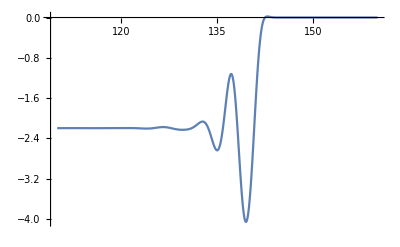

jeListepsv3.csv

{{110,-2.19723},{130.,-2.22798},{150.,4.2581×10^-11}}

```mathematica
integ[start_,end_]:=lx/δk*NIntegrate[(τ-τe)*(ρϵ[τ,0]-ρ0299[τ,0]),{τ,start,end}]
oldJe=integ[110,160];
jeListϵ={{110,oldJe}};
Do[
newJe=oldJe-integ[110+i,110+i+δ];
AppendTo[jeListϵ,{(110+i+δ),newJe}];
oldJe=newJe;
Print[i];
,{i,0.,50-δ,δ}]
ListLinePlot[jeListϵ]
Export["jeListepsv3.csv",jeListϵ]
```

```mathematica
jeListψ1New=Mod[jeListψ1,1]
jeListψ2New=Mod[jeListψ2,1]
jeListϵNew=Mod[jeListϵ,1]
```

```mathematica
(*Export["jeListepsmodv3.csv",jeListϵNew]*)
```

jeList1v2.csv

jeListsigma1v2.csv

jeListsigma2v2.csv

jeListpsi1v2.csv

jeListpsi2v2.csv

jeListepsv2.csv

jeListpsi1modv2.csv

jeListpsi2modv2.csv

jeListepsmodv2.csv

```mathematica
lx/(2π)*jeListϵ
```

{{1210/π,-1.59725},{388.656,-1.59714},{423.67,-1.59676},{458.685,-1.57853},{493.699,-0.0840391},{528.713,-0.0840391}}